```mathematica
ClearAll["Global`*"]
```

```mathematica
n = 40
y = {-2.57251482,0.33806206,2.71757796,1.09861336,2.85603752,-0.91651351,0.15555127,-2.68160347,2.47043789,3.47459025,1.63949862,-1.32148757,2.64187513,0.30357848,-4.09546231,-1.50709863,-0.99517866,-2.0648892,-2.40317949,3.46383544,0.91173696,1.18222221,0.04235722,-0.52815171,1.15551598,-1.62749724,0.71473237,-1.08458812,4.66020296,1.24563831,-0.67970862,0.93461681,1.18187607,-1.49501051,2.44755622,-2.06424237,-0.04584074,1.93396696,1.07685273,-0.09837907}
```

40

{-2.57251,0.338062,2.71758,1.09861,2.85604,-0.916514,0.155551,-2.6816,2.47044,3.47459,1.6395,-1.32149,2.64188,0.303578,-4.09546,-1.5071,-0.995179,-2.06489,-2.40318,3.46384,0.911737,1.18222,0.0423572,-0.528152,1.15552,-1.6275,0.714732,-1.08459,4.6602,1.24564,-0.679709,0.934617,1.18188,-1.49501,2.44756,-2.06424,-0.0458407,1.93397,1.07685,-0.0983791}

```mathematica
epslist = N[Range[ -1,1,(1-(-1))/50]]
```

{-1.,-0.96,-0.92,-0.88,-0.84,-0.8,-0.76,-0.72,-0.68,-0.64,-0.6,-0.56,-0.52,-0.48,-0.44,-0.4,-0.36,-0.32,-0.28,-0.24,-0.2,-0.16,-0.12,-0.08,-0.04,0.,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.68,0.72,0.76,0.8,0.84,0.88,0.92,0.96,1.}

```mathematica
pmu1[mu1_]:=PDF[NormalDistribution[0,5], mu1]*Boole[-2<= mu1 && mu1 <= 2]
```

```mathematica
pmu2[mu2_]:=PDF[NormalDistribution[0,5], mu2]*Boole[-2<= mu2 && mu2 <= 2]
```

```mathematica
pmu3[mu3_, eps1_, eps2_]:=PDF[NormalDistribution[0+eps1,5+eps2], mu3]*Boole[-2<= mu3 && mu3 <= 2]
```

```mathematica
pu[mu1_, mu2_, mu3_, eps1_, eps2_]:=pmu1[mu1] * pmu2[mu2] * pmu3[mu3,eps1, eps2]
```

```mathematica
NArgMax[pu[mu1, mu2, mu3, eps1=0,eps2=0], {mu1,-5,5},{mu2,-5,5},{mu3,-5,5}, WorkingPrecision->100]
```

NArgMax::nonopt: Options expected (instead of {mu3,-5,5}) beyond position 2 in NArgMax[(ⅇ^(-mu1^2/50-mu2^2/50-mu3^2/50) Boole[-2≤mu1&&mu1≤2] Boole[-2≤mu2&&mu2≤2] Boole[-2≤mu3&&mu3≤2])/(250 √2 π^(3/2)),{mu1,-5,5},{mu2,-5,5},{mu3,-5,5},WorkingPrecision→100]. An option must be a rule or a list of rules.

NArgMax[1/(250 √2 π^(3/2))ⅇ^(-mu1^2/50-mu2^2/50-mu3^2/50) Boole[-2≤mu1&&mu1≤2] Boole[-2≤mu2&&mu2≤2] Boole[-2≤mu3&&mu3≤2],{mu1,-5,5},{mu2,-5,5},{mu3,-5,5},WorkingPrecision→100]

```mathematica
L[mu1_, mu2_, mu3_, y_]:= PDF[NormalDistribution[3.0*mu1*mu2-mu3,1],y]
```

```mathematica
For[i=1, i<=n,i++, 
pu[mu1_, mu2_, mu3_, eps1_, eps2_]=pu[mu1, mu2, mu3,eps1, eps2] * L[mu1, mu2, mu3, y[[i]]];
]
```

```mathematica
norm = NIntegrate[pu[mu1,mu2,mu3, eps1=0,eps2=0],{mu1,-2,2},{mu2,-2,2}, {mu3,-2,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.53745×10^-52 and 1.63239×10^-57 for the integral and error estimates.

1.53745×10^-52

```mathematica
p[mu1_,mu2_,mu3_]:= pu[mu1, mu2, mu3, eps1=0, eps2=0]/ norm
```

```mathematica
ArgMax[p[mu1,mu2,mu3],{mu1,mu2,mu3}]
```

{-0.000106377,-0.000106274,-0.311331}

```mathematica
mu3Range = Range[-2,2,0.02];
```

```mathematica
{t, mu3Table}= Timing[ Table[NIntegrate[p[mu1,mu2,mu3], {mu1, -∞, ∞}, {mu2, -∞, ∞}], {mu3, mu3Range}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{205.526,{0.270859,0.273011,0.275187,0.277386,0.27961,0.281858,0.284132,0.286432,0.288758,0.291112,0.293494,0.295905,0.298346,0.300817,0.30332,0.305854,0.308423,0.311025,0.313663,0.316337,0.319048,0.321798,0.324589,0.32742,0.330295,0.333213,0.336178,0.33919,0.342251,0.345364,0.34853,0.35175,0.355029,0.358367,0.361768,0.365234,0.368768,0.372373,0.376053,0.379811,0.383651,0.387577,0.391595,0.395708,0.399923,0.404245,0.408681,0.413238,0.417925,0.42275,0.427723,0.432856,0.438161,0.443654,0.449351,0.455271,0.461437,0.467874,0.474612,0.481682,0.489123,0.496976,0.505286,0.514099,0.523466,0.533432,0.544041,0.555328,0.567315,0.580003,0.59337,0.607364,0.621895,0.636833,0.652006,0.667198,0.682154,0.696585,0.710179,0.722612,0.733563,0.742733,0.749857,0.754725,0.757187,0.757172,0.754683,0.749804,0.742688,0.733556,0.722675,0.710349,0.696898,0.682645,0.667899,0.652947,0.638036,0.623379,0.609141,0.595447,0.582382,0.569994,0.558303,0.547303,0.536972,0.527273,0.518164,0.509596,0.501521,0.493893,0.486667,0.479803,0.473263,0.467017,0.461035,0.455292,0.449767,0.444441,0.439298,0.434322,0.429502,0.424826,0.420285,0.415869,0.411572,0.407385,0.403303,0.399319,0.395428,0.391625,0.387906,0.384266,0.380703,0.377211,0.373789,0.370432,0.367138,0.363904,0.360729,0.357608,0.354541,0.351525,0.348558,0.345639,0.342765,0.339936,0.337148,0.334402,0.331696,0.329027,0.326396,0.323801,0.321241,0.318714,0.31622,0.313757,0.311326,0.308924,0.306551,0.304207,0.30189,0.2996,0.297335,0.295096,0.292882,0.290692,0.288525,0.286382,0.28426,0.282161,0.280082,0.278025,0.275987,0.27397,0.271972,0.269993,0.268033,0.266091,0.264167,0.26226,0.260371,0.258498,0.256641,0.254801,0.252977,0.251168,0.249375,0.247596,0.245832,0.244083,0.242347,0.240626,0.238918,0.237224,0.235544,0.233876,0.232221,0.230578,0.228949,0.227331,0.225725}}

```mathematica
mu3norm = Total[mu3Table]
mu3Table = mu3Table/mu3norm
mu3TrueCDF= Table[Function[upto,Sum[mu3Table[[i]], {i, 1,upto}]][i], {i,1, Length[mu3Table]}]
```

82.3947

{0.00328733,0.00331346,0.00333986,0.00336656,0.00339354,0.00342083,0.00344843,0.00347634,0.00350457,0.00353314,0.00356205,0.00359131,0.00362094,0.00365093,0.0036813,0.00371207,0.00374323,0.00377482,0.00380683,0.00383928,0.00387219,0.00390557,0.00393944,0.0039738,0.00400869,0.00404411,0.00408009,0.00411665,0.0041538,0.00419158,0.00423,0.00426909,0.00430888,0.0043494,0.00439067,0.00443273,0.00447562,0.00451938,0.00456404,0.00460965,0.00465626,0.00470391,0.00475267,0.00480259,0.00485374,0.0049062,0.00496004,0.00501535,0.00507223,0.00513079,0.00519115,0.00525344,0.00531783,0.0053845,0.00545364,0.00552549,0.00560033,0.00567845,0.00576022,0.00584604,0.00593635,0.00603166,0.0061325,0.00623947,0.00635315,0.0064741,0.00660287,0.00673986,0.00688533,0.00703932,0.00720156,0.0073714,0.00754775,0.00772905,0.0079132,0.00809758,0.0082791,0.00845425,0.00861924,0.00877013,0.00890304,0.00901433,0.0091008,0.00915987,0.00918976,0.00918957,0.00915937,0.00910014,0.00901379,0.00890295,0.0087709,0.00862129,0.00845804,0.00828506,0.0081061,0.00792462,0.00774366,0.00756577,0.00739296,0.00722677,0.0070682,0.00691785,0.00677596,0.00664246,0.00651707,0.00639936,0.0062888,0.00618481,0.00608682,0.00599423,0.00590653,0.00582322,0.00574386,0.00566805,0.00559544,0.00552575,0.00545869,0.00539405,0.00533163,0.00527123,0.00521274,0.00515599,0.00510087,0.00504729,0.00499513,0.00494431,0.00489477,0.00484641,0.00479919,0.00475304,0.0047079,0.00466373,0.00462048,0.0045781,0.00453656,0.00449582,0.00445584,0.0044166,0.00437806,0.00434018,0.00430296,0.00426636,0.00423035,0.00419492,0.00416004,0.0041257,0.00409187,0.00405854,0.00402569,0.00399331,0.00396138,0.00392988,0.0038988,0.00386814,0.00383787,0.00380798,0.00377847,0.00374932,0.00372052,0.00369207,0.00366395,0.00363615,0.00360867,0.0035815,0.00355463,0.00352804,0.00350175,0.00347573,0.00344998,0.0034245,0.00339927,0.0033743,0.00334958,0.00332509,0.00330085,0.00327683,0.00325304,0.00322947,0.00320611,0.00318297,0.00316004,0.00313731,0.00311478,0.00309245,0.00307031,0.00304835,0.00302659,0.003005,0.00298359,0.00296236,0.0029413,0.00292041,0.00289968,0.00287912,0.00285872,0.00283848,0.0028184,0.00279846,0.00277868,0.00275905,0.00273956}

{0.00328733,0.00660079,0.00994065,0.0133072,0.0167008,0.0201216,0.02357,0.0270463,0.0305509,0.0340841,0.0376461,0.0412374,0.0448584,0.0485093,0.0521906,0.0559027,0.0596459,0.0634207,0.0672275,0.0710668,0.074939,0.0788446,0.082784,0.0867578,0.0907665,0.0948106,0.0988907,0.103007,0.107161,0.111353,0.115583,0.119852,0.124161,0.12851,0.132901,0.137334,0.141809,0.146329,0.150893,0.155502,0.160158,0.164862,0.169615,0.174418,0.179271,0.184178,0.189138,0.194153,0.199225,0.204356,0.209547,0.214801,0.220118,0.225503,0.230957,0.236482,0.242082,0.247761,0.253521,0.259367,0.265303,0.271335,0.277468,0.283707,0.29006,0.296534,0.303137,0.309877,0.316762,0.323802,0.331003,0.338375,0.345922,0.353651,0.361565,0.369662,0.377941,0.386396,0.395015,0.403785,0.412688,0.421702,0.430803,0.439963,0.449153,0.458342,0.467502,0.476602,0.485616,0.494519,0.503289,0.511911,0.520369,0.528654,0.53676,0.544685,0.552428,0.559994,0.567387,0.574614,0.581682,0.5886,0.595376,0.602018,0.608535,0.614935,0.621223,0.627408,0.633495,0.639489,0.645396,0.651219,0.656963,0.662631,0.668226,0.673752,0.679211,0.684605,0.689937,0.695208,0.700421,0.705577,0.710677,0.715725,0.72072,0.725664,0.730559,0.735405,0.740204,0.744958,0.749665,0.754329,0.75895,0.763528,0.768064,0.77256,0.777016,0.781433,0.785811,0.790151,0.794454,0.79872,0.80295,0.807145,0.811305,0.815431,0.819523,0.823582,0.827607,0.831601,0.835562,0.839492,0.843391,0.847259,0.851097,0.854905,0.858683,0.862432,0.866153,0.869845,0.873509,0.877145,0.880754,0.884335,0.88789,0.891418,0.89492,0.898395,0.901845,0.90527,0.908669,0.912043,0.915393,0.918718,0.922019,0.925296,0.928549,0.931778,0.934984,0.938167,0.941327,0.944465,0.947579,0.950672,0.953742,0.956791,0.959817,0.962822,0.965806,0.968768,0.971709,0.97463,0.97753,0.980409,0.983267,0.986106,0.988924,0.991723,0.994501,0.99726,1.}

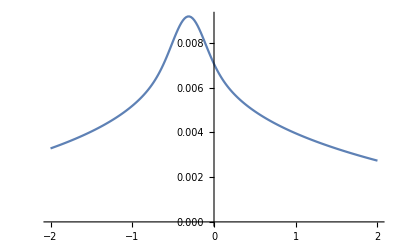

```mathematica
ListLinePlot[Transpose[{mu3Range,mu3Table}],PlotRange->{Automatic,Full}]
```

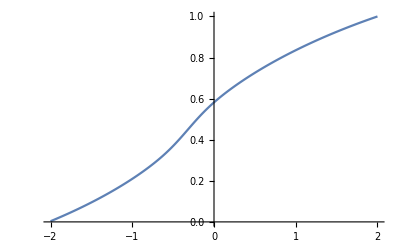

```mathematica
ListLinePlot[Transpose[{mu3Range,mu3TrueCDF}],PlotRange->{Automatic,Full}]
```

```mathematica
matrix = Table[0,{r,Length[mu3Range]},{c, Length[epslist]}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
For[i = 1, i <= Length[epslist], i++,
 eps = epslist[[i]];
 norm = NIntegrate[pu[mu1, mu2, mu3, eps1 = eps, eps2 = 0], {mu1, -2, 2}, {mu2, -2, 2}, {mu3, -2, 2}];
 p[mu1_, mu2_, mu3_] := pu[mu1, mu2, mu3, eps1=eps, eps2=0]/ norm;
mu3Table=  Table[NIntegrate[p[mu1,mu2,mu3], {mu1, -∞, ∞}, {mu2, -∞, ∞}], {mu3, mu3Range}];
mu3norm = Total[mu3Table];
mu3Table = mu3Table/mu3norm;
mu3CDF= Table[Function[upto,Sum[mu3Table[[i]], {i, 1,upto}]][i], {i,1, Length[mu3Table]}];
matrix[[All,i]] = mu3CDF;
 ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.52606×10^-52 and 1.09397×10^-57 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.52768×10^-52 and 1.09439×10^-57 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.5292×10^-52 and 1.09387×10^-57 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
MatrixForm[matrix]
```

(0.00354223 | 0.00353177 | 0.00352133 | 0.00351092 | 0.00350053 | 0.00349016 | 0.00347981 | 0.00346949 | 0.00345918 | 0.0034489 | 0.00343864 | 0.0034284 | 0.00341818 | 0.00340799 | 0.00339782 | 0.00338766 | 0.00337753 | 0.00336742 | 0.00335734 | 0.00334727 | 0.00333723 | 0.00332721 | 0.00331721 | 0.00330723 | 0.00329727 | 0.00328733 | 0.00327742 | 0.00326753 | 0.00325765 | 0.0032478 | 0.00323797 | 0.00322817 | 0.00321838 | 0.00320862 | 0.00319887 | 0.00318915 | 0.00317945 | 0.00316977 | 0.00316011 | 0.00315048 | 0.00314086 | 0.00313127 | 0.0031217 | 0.00311214 | 0.00310261 | 0.00309311 | 0.00308362 | 0.00307415 | 0.0030647 | 0.00305528 | 0.00304588
0.00710975 | 0.00708887 | 0.00706804 | 0.00704725 | 0.00702651 | 0.00700581 | 0.00698515 | 0.00696453 | 0.00694396 | 0.00692343 | 0.00690295 | 0.0068825 | 0.0068621 | 0.00684174 | 0.00682143 | 0.00680116 | 0.00678093 | 0.00676074 | 0.0067406 | 0.0067205 | 0.00670044 | 0.00668043 | 0.00666045 | 0.00664052 | 0.00662064 | 0.00660079 | 0.00658099 | 0.00656123 | 0.00654151 | 0.00652184 | 0.0065022 | 0.00648262 | 0.00646307 | 0.00644356 | 0.0064241 | 0.00640468 | 0.0063853 | 0.00636596 | 0.00634667 | 0.00632742 | 0.00630821 | 0.00628904 | 0.00626991 | 0.00625083 | 0.00623179 | 0.00621279 | 0.00619383 | 0.00617491 | 0.00615604 | 0.00613721 | 0.00611842
0.0107028 | 0.0106716 | 0.0106404 | 0.0106093 | 0.0105782 | 0.0105472 | 0.0105163 | 0.0104854 | 0.0104546 | 0.0104239 | 0.0103932 | 0.0103626 | 0.010332 | 0.0103015 | 0.0102711 | 0.0102408 | 0.0102105 | 0.0101802 | 0.0101501 | 0.01012 | 0.0100899 | 0.0100599 | 0.01003 | 0.0100002 | 0.00997038 | 0.00994065 | 0.00991099 | 0.00988139 | 0.00985186 | 0.00982239 | 0.00979298 | 0.00976363 | 0.00973434 | 0.00970512 | 0.00967596 | 0.00964687 | 0.00961783 | 0.00958886 | 0.00955995 | 0.00953111 | 0.00950233 | 0.00947361 | 0.00944495 | 0.00941635 | 0.00938782 | 0.00935935 | 0.00933094 | 0.00930259 | 0.0092743 | 0.00924608 | 0.00921792
0.0143217 | 0.0142801 | 0.0142386 | 0.0141972 | 0.0141559 | 0.0141146 | 0.0140735 | 0.0140324 | 0.0139914 | 0.0139505 | 0.0139096 | 0.0138689 | 0.0138282 | 0.0137876 | 0.0137471 | 0.0137067 | 0.0136664 | 0.0136262 | 0.013586 | 0.0135459 | 0.0135059 | 0.013466 | 0.0134262 | 0.0133864 | 0.0133468 | 0.0133072 | 0.0132677 | 0.0132283 | 0.013189 | 0.0131497 | 0.0131106 | 0.0130715 | 0.0130325 | 0.0129936 | 0.0129548 | 0.012916 | 0.0128773 | 0.0128388 | 0.0128003 | 0.0127619 | 0.0127235 | 0.0126853 | 0.0126471 | 0.012609 | 0.012571 | 0.0125331 | 0.0124952 | 0.0124575 | 0.0124198 | 0.0123822 | 0.0123447
0.0179667 | 0.0179148 | 0.017863 | 0.0178114 | 0.0177598 | 0.0177083 | 0.017657 | 0.0176057 | 0.0175546 | 0.0175035 | 0.0174526 | 0.0174017 | 0.017351 | 0.0173003 | 0.0172498 | 0.0171994 | 0.017149 | 0.0170988 | 0.0170487 | 0.0169987 | 0.0169488 | 0.016899 | 0.0168493 | 0.0167997 | 0.0167502 | 0.0167008 | 0.0166515 | 0.0166023 | 0.0165532 | 0.0165042 | 0.0164553 | 0.0164065 | 0.0163578 | 0.0163093 | 0.0162608 | 0.0162124 | 0.0161642 | 0.016116 | 0.0160679 | 0.01602 | 0.0159721 | 0.0159243 | 0.0158767 | 0.0158291 | 0.0157817 | 0.0157343 | 0.0156871 | 0.0156399 | 0.0155929 | 0.0155459 | 0.0154991
0.0216381 | 0.0215759 | 0.0215139 | 0.021452 | 0.0213903 | 0.0213286 | 0.0212671 | 0.0212057 | 0.0211444 | 0.0210833 | 0.0210223 | 0.0209614 | 0.0209006 | 0.0208399 | 0.0207794 | 0.020719 | 0.0206587 | 0.0205985 | 0.0205385 | 0.0204785 | 0.0204187 | 0.0203591 | 0.0202995 | 0.0202401 | 0.0201808 | 0.0201216 | 0.0200625 | 0.0200036 | 0.0199448 | 0.019886 | 0.0198275 | 0.019769 | 0.0197107 | 0.0196525 | 0.0195944 | 0.0195364 | 0.0194785 | 0.0194208 | 0.0193632 | 0.0193057 | 0.0192484 | 0.0191911 | 0.019134 | 0.019077 | 0.0190201 | 0.0189633 | 0.0189067 | 0.0188502 | 0.0187938 | 0.0187375 | 0.0186813
0.0253361 | 0.0252637 | 0.0251915 | 0.0251195 | 0.0250476 | 0.0249758 | 0.0249042 | 0.0248327 | 0.0247613 | 0.0246901 | 0.024619 | 0.0245481 | 0.0244773 | 0.0244067 | 0.0243362 | 0.0242658 | 0.0241956 | 0.0241255 | 0.0240556 | 0.0239858 | 0.0239162 | 0.0238466 | 0.0237773 | 0.023708 | 0.023639 | 0.02357 | 0.0235012 | 0.0234325 | 0.023364 | 0.0232956 | 0.0232274 | 0.0231593 | 0.0230913 | 0.0230235 | 0.0229558 | 0.0228883 | 0.0228209 | 0.0227536 | 0.0226865 | 0.0226195 | 0.0225526 | 0.0224859 | 0.0224194 | 0.0223529 | 0.0222867 | 0.0222205 | 0.0221545 | 0.0220886 | 0.0220229 | 0.0219573 | 0.0218918
0.0290611 | 0.0289785 | 0.0288962 | 0.028814 | 0.028732 | 0.0286501 | 0.0285684 | 0.0284869 | 0.0284055 | 0.0283242 | 0.0282432 | 0.0281623 | 0.0280815 | 0.0280009 | 0.0279205 | 0.0278402 | 0.0277601 | 0.0276802 | 0.0276004 | 0.0275208 | 0.0274413 | 0.027362 | 0.0272828 | 0.0272039 | 0.027125 | 0.0270463 | 0.0269678 | 0.0268895 | 0.0268113 | 0.0267332 | 0.0266554 | 0.0265776 | 0.0265001 | 0.0264227 | 0.0263454 | 0.0262683 | 0.0261914 | 0.0261146 | 0.026038 | 0.0259616 | 0.0258853 | 0.0258091 | 0.0257331 | 0.0256573 | 0.0255816 | 0.0255061 | 0.0254308 | 0.0253556 | 0.0252805 | 0.0252057 | 0.0251309
0.0328133 | 0.0327206 | 0.0326282 | 0.0325359 | 0.0324438 | 0.0323519 | 0.0322602 | 0.0321686 | 0.0320772 | 0.031986 | 0.031895 | 0.0318042 | 0.0317135 | 0.031623 | 0.0315327 | 0.0314425 | 0.0313526 | 0.0312628 | 0.0311732 | 0.0310838 | 0.0309945 | 0.0309054 | 0.0308166 | 0.0307278 | 0.0306393 | 0.0305509 | 0.0304627 | 0.0303747 | 0.0302869 | 0.0301992 | 0.0301117 | 0.0300244 | 0.0299373 | 0.0298503 | 0.0297636 | 0.029677 | 0.0295905 | 0.0295043 | 0.0294182 | 0.0293323 | 0.0292466 | 0.029161 | 0.0290756 | 0.0289904 | 0.0289054 | 0.0288206 | 0.0287359 | 0.0286514 | 0.0285671 | 0.0284829 | 0.0283989
0.0365931 | 0.0364904 | 0.0363879 | 0.0362855 | 0.0361834 | 0.0360815 | 0.0359798 | 0.0358783 | 0.0357769 | 0.0356758 | 0.0355748 | 0.0354741 | 0.0353735 | 0.0352732 | 0.035173 | 0.0350731 | 0.0349733 | 0.0348737 | 0.0347743 | 0.0346751 | 0.0345761 | 0.0344773 | 0.0343787 | 0.0342803 | 0.0341821 | 0.0340841 | 0.0339862 | 0.0338886 | 0.0337912 | 0.0336939 | 0.0335968 | 0.0335 | 0.0334033 | 0.0333068 | 0.0332106 | 0.0331145 | 0.0330186 | 0.0329229 | 0.0328274 | 0.032732 | 0.0326369 | 0.032542 | 0.0324472 | 0.0323527 | 0.0322583 | 0.0321642 | 0.0320702 | 0.0319764 | 0.0318828 | 0.0317894 | 0.0316962
0.0404007 | 0.040288 | 0.0401755 | 0.0400632 | 0.0399511 | 0.0398392 | 0.0397275 | 0.0396161 | 0.0395049 | 0.0393938 | 0.039283 | 0.0391724 | 0.039062 | 0.0389518 | 0.0388419 | 0.0387321 | 0.0386225 | 0.0385132 | 0.0384041 | 0.0382952 | 0.0381865 | 0.038078 | 0.0379697 | 0.0378616 | 0.0377538 | 0.0376461 | 0.0375387 | 0.0374315 | 0.0373244 | 0.0372176 | 0.037111 | 0.0370046 | 0.0368985 | 0.0367925 | 0.0366868 | 0.0365812 | 0.0364759 | 0.0363707 | 0.0362658 | 0.0361611 | 0.0360566 | 0.0359523 | 0.0358483 | 0.0357444 | 0.0356407 | 0.0355373 | 0.035434 | 0.035331 | 0.0352282 | 0.0351256 | 0.0350232
0.0442366 | 0.0441139 | 0.0439914 | 0.0438692 | 0.0437472 | 0.0436254 | 0.0435038 | 0.0433825 | 0.0432614 | 0.0431405 | 0.0430198 | 0.0428994 | 0.0427792 | 0.0426593 | 0.0425395 | 0.04242 | 0.0423007 | 0.0421817 | 0.0420629 | 0.0419443 | 0.0418259 | 0.0417077 | 0.0415898 | 0.0414721 | 0.0413547 | 0.0412374 | 0.0411204 | 0.0410036 | 0.0408871 | 0.0407708 | 0.0406547 | 0.0405388 | 0.0404231 | 0.0403077 | 0.0401925 | 0.0400775 | 0.0399628 | 0.0398483 | 0.039734 | 0.0396199 | 0.0395061 | 0.0393925 | 0.0392791 | 0.0391659 | 0.039053 | 0.0389403 | 0.0388278 | 0.0387155 | 0.0386035 | 0.0384917 | 0.0383801
0.048101 | 0.0479684 | 0.047836 | 0.0477039 | 0.047572 | 0.0474403 | 0.0473089 | 0.0471777 | 0.0470468 | 0.0469161 | 0.0467857 | 0.0466555 | 0.0465255 | 0.0463958 | 0.0462664 | 0.0461372 | 0.0460082 | 0.0458795 | 0.045751 | 0.0456227 | 0.0454947 | 0.045367 | 0.0452395 | 0.0451122 | 0.0449852 | 0.0448584 | 0.0447318 | 0.0446055 | 0.0444795 | 0.0443537 | 0.0442281 | 0.0441028 | 0.0439777 | 0.0438528 | 0.0437282 | 0.0436039 | 0.0434797 | 0.0433559 | 0.0432322 | 0.0431088 | 0.0429857 | 0.0428628 | 0.0427401 | 0.0426177 | 0.0424955 | 0.0423735 | 0.0422518 | 0.0421304 | 0.0420092 | 0.0418882 | 0.0417674
0.0519943 | 0.0518518 | 0.0517096 | 0.0515676 | 0.0514258 | 0.0512844 | 0.0511432 | 0.0510022 | 0.0508615 | 0.0507211 | 0.0505809 | 0.050441 | 0.0503013 | 0.0501619 | 0.0500228 | 0.0498839 | 0.0497453 | 0.0496069 | 0.0494688 | 0.049331 | 0.0491934 | 0.049056 | 0.048919 | 0.0487821 | 0.0486456 | 0.0485093 | 0.0483733 | 0.0482375 | 0.048102 | 0.0479667 | 0.0478317 | 0.0476969 | 0.0475624 | 0.0474282 | 0.0472942 | 0.0471605 | 0.047027 | 0.0468938 | 0.0467609 | 0.0466282 | 0.0464958 | 0.0463636 | 0.0462317 | 0.0461 | 0.0459686 | 0.0458375 | 0.0457066 | 0.0455759 | 0.0454456 | 0.0453154 | 0.0451856
0.0559169 | 0.0557645 | 0.0556125 | 0.0554607 | 0.0553092 | 0.0551579 | 0.055007 | 0.0548563 | 0.0547059 | 0.0545557 | 0.0544058 | 0.0542562 | 0.0541069 | 0.0539579 | 0.0538091 | 0.0536606 | 0.0535124 | 0.0533644 | 0.0532167 | 0.0530693 | 0.0529222 | 0.0527753 | 0.0526287 | 0.0524824 | 0.0523364 | 0.0521906 | 0.0520451 | 0.0518999 | 0.0517549 | 0.0516102 | 0.0514658 | 0.0513217 | 0.0511778 | 0.0510343 | 0.0508909 | 0.0507479 | 0.0506051 | 0.0504626 | 0.0503204 | 0.0501784 | 0.0500368 | 0.0498954 | 0.0497542 | 0.0496133 | 0.0494728 | 0.0493324 | 0.0491924 | 0.0490526 | 0.0489131 | 0.0487739 | 0.0486349
0.0598691 | 0.059707 | 0.0595451 | 0.0593836 | 0.0592223 | 0.0590614 | 0.0589007 | 0.0587403 | 0.0585802 | 0.0584204 | 0.0582609 | 0.0581017 | 0.0579427 | 0.0577841 | 0.0576257 | 0.0574676 | 0.0573098 | 0.0571523 | 0.0569951 | 0.0568382 | 0.0566816 | 0.0565252 | 0.0563691 | 0.0562134 | 0.0560579 | 0.0559027 | 0.0557477 | 0.0555931 | 0.0554388 | 0.0552847 | 0.055131 | 0.0549775 | 0.0548243 | 0.0546714 | 0.0545188 | 0.0543664 | 0.0542144 | 0.0540626 | 0.0539111 | 0.05376 | 0.0536091 | 0.0534584 | 0.0533081 | 0.0531581 | 0.0530083 | 0.0528589 | 0.0527097 | 0.0525608 | 0.0524122 | 0.0522639 | 0.0521158
0.0638512 | 0.0636794 | 0.0635079 | 0.0633366 | 0.0631657 | 0.0629951 | 0.0628248 | 0.0626547 | 0.062485 | 0.0623156 | 0.0621465 | 0.0619777 | 0.0618092 | 0.0616409 | 0.061473 | 0.0613054 | 0.0611381 | 0.0609711 | 0.0608044 | 0.060638 | 0.0604719 | 0.0603061 | 0.0601406 | 0.0599754 | 0.0598105 | 0.0596459 | 0.0594816 | 0.0593176 | 0.0591539 | 0.0589905 | 0.0588274 | 0.0586646 | 0.0585022 | 0.05834 | 0.0581781 | 0.0580165 | 0.0578552 | 0.0576942 | 0.0575335 | 0.0573732 | 0.0572131 | 0.0570533 | 0.0568938 | 0.0567346 | 0.0565758 | 0.0564172 | 0.0562589 | 0.0561009 | 0.0559432 | 0.0557859 | 0.0556288
0.0678638 | 0.0676823 | 0.0675011 | 0.0673202 | 0.0671397 | 0.0669594 | 0.0667795 | 0.0665999 | 0.0664206 | 0.0662416 | 0.066063 | 0.0658846 | 0.0657066 | 0.0655288 | 0.0653514 | 0.0651743 | 0.0649976 | 0.0648211 | 0.0646449 | 0.0644691 | 0.0642936 | 0.0641184 | 0.0639435 | 0.0637689 | 0.0635947 | 0.0634207 | 0.0632471 | 0.0630738 | 0.0629008 | 0.0627281 | 0.0625557 | 0.0623836 | 0.0622119 | 0.0620405 | 0.0618694 | 0.0616986 | 0.0615281 | 0.0613579 | 0.061188 | 0.0610185 | 0.0608493 | 0.0606803 | 0.0605117 | 0.0603435 | 0.0601755 | 0.0600078 | 0.0598405 | 0.0596734 | 0.0595067 | 0.0593403 | 0.0591742
0.0719072 | 0.071716 | 0.0715253 | 0.0713348 | 0.0711447 | 0.0709549 | 0.0707654 | 0.0705762 | 0.0703874 | 0.0701989 | 0.0700107 | 0.0698229 | 0.0696354 | 0.0694482 | 0.0692614 | 0.0690748 | 0.0688886 | 0.0687027 | 0.0685172 | 0.068332 | 0.0681471 | 0.0679625 | 0.0677783 | 0.0675944 | 0.0674108 | 0.0672275 | 0.0670446 | 0.066862 | 0.0666797 | 0.0664978 | 0.0663162 | 0.0661349 | 0.0659539 | 0.0657733 | 0.065593 | 0.065413 | 0.0652334 | 0.065054 | 0.064875 | 0.0646964 | 0.064518 | 0.06434 | 0.0641623 | 0.063985 | 0.0638079 | 0.0636312 | 0.0634549 | 0.0632788 | 0.0631031 | 0.0629277 | 0.0627526
0.0759817 | 0.0757811 | 0.0755807 | 0.0753807 | 0.0751811 | 0.0749818 | 0.0747828 | 0.0745842 | 0.0743859 | 0.0741879 | 0.0739903 | 0.073793 | 0.0735961 | 0.0733995 | 0.0732032 | 0.0730073 | 0.0728117 | 0.0726165 | 0.0724216 | 0.072227 | 0.0720328 | 0.0718389 | 0.0716454 | 0.0714522 | 0.0712593 | 0.0710668 | 0.0708746 | 0.0706828 | 0.0704913 | 0.0703002 | 0.0701093 | 0.0699189 | 0.0697287 | 0.0695389 | 0.0693495 | 0.0691604 | 0.0689716 | 0.0687831 | 0.068595 | 0.0684073 | 0.0682199 | 0.0680328 | 0.0678461 | 0.0676597 | 0.0674736 | 0.0672879 | 0.0671025 | 0.0669175 | 0.0667328 | 0.0665484 | 0.0663644
0.0800879 | 0.0798778 | 0.0796679 | 0.0794585 | 0.0792493 | 0.0790406 | 0.0788322 | 0.0786241 | 0.0784164 | 0.078209 | 0.078002 | 0.0777953 | 0.077589 | 0.0773831 | 0.0771775 | 0.0769722 | 0.0767673 | 0.0765628 | 0.0763586 | 0.0761547 | 0.0759512 | 0.0757481 | 0.0755453 | 0.0753428 | 0.0751408 | 0.074939 | 0.0747376 | 0.0745366 | 0.0743359 | 0.0741356 | 0.0739356 | 0.073736 | 0.0735367 | 0.0733378 | 0.0731392 | 0.072941 | 0.0727432 | 0.0725456 | 0.0723485 | 0.0721517 | 0.0719552 | 0.0717591 | 0.0715634 | 0.071368 | 0.0711729 | 0.0709782 | 0.0707839 | 0.0705899 | 0.0703962 | 0.070203 | 0.07001
0.0842262 | 0.0840066 | 0.0837874 | 0.0835685 | 0.0833499 | 0.0831318 | 0.082914 | 0.0826965 | 0.0824794 | 0.0822627 | 0.0820464 | 0.0818304 | 0.0816147 | 0.0813995 | 0.0811846 | 0.08097 | 0.0807559 | 0.080542 | 0.0803286 | 0.0801155 | 0.0799028 | 0.0796904 | 0.0794784 | 0.0792668 | 0.0790555 | 0.0788446 | 0.078634 | 0.0784239 | 0.078214 | 0.0780046 | 0.0777955 | 0.0775868 | 0.0773784 | 0.0771704 | 0.0769628 | 0.0767555 | 0.0765486 | 0.076342 | 0.0761359 | 0.07593 | 0.0757246 | 0.0755195 | 0.0753148 | 0.0751104 | 0.0749064 | 0.0747028 | 0.0744995 | 0.0742966 | 0.074094 | 0.0738919 | 0.07369
0.0883971 | 0.0881681 | 0.0879394 | 0.0877112 | 0.0874833 | 0.0872558 | 0.0870287 | 0.0868019 | 0.0865755 | 0.0863495 | 0.0861238 | 0.0858986 | 0.0856737 | 0.0854491 | 0.085225 | 0.0850012 | 0.0847778 | 0.0845548 | 0.0843321 | 0.0841099 | 0.0838879 | 0.0836664 | 0.0834453 | 0.0832245 | 0.0830041 | 0.082784 | 0.0825644 | 0.0823451 | 0.0821262 | 0.0819076 | 0.0816895 | 0.0814717 | 0.0812543 | 0.0810372 | 0.0808206 | 0.0806043 | 0.0803884 | 0.0801728 | 0.0799577 | 0.0797429 | 0.0795284 | 0.0793144 | 0.0791007 | 0.0788875 | 0.0786745 | 0.078462 | 0.0782498 | 0.078038 | 0.0778266 | 0.0776156 | 0.0774049
0.0926009 | 0.0923626 | 0.0921247 | 0.0918871 | 0.0916499 | 0.0914131 | 0.0911767 | 0.0909407 | 0.090705 | 0.0904698 | 0.0902349 | 0.0900004 | 0.0897663 | 0.0895326 | 0.0892992 | 0.0890663 | 0.0888337 | 0.0886015 | 0.0883697 | 0.0881383 | 0.0879072 | 0.0876766 | 0.0874463 | 0.0872164 | 0.0869869 | 0.0867578 | 0.0865291 | 0.0863008 | 0.0860728 | 0.0858452 | 0.085618 | 0.0853912 | 0.0851648 | 0.0849388 | 0.0847131 | 0.0844879 | 0.084263 | 0.0840385 | 0.0838144 | 0.0835907 | 0.0833673 | 0.0831444 | 0.0829218 | 0.0826997 | 0.0824779 | 0.0822565 | 0.0820354 | 0.0818148 | 0.0815946 | 0.0813747 | 0.0811552
0.0968383 | 0.0965907 | 0.0963435 | 0.0960967 | 0.0958503 | 0.0956043 | 0.0953587 | 0.0951134 | 0.0948686 | 0.0946241 | 0.0943801 | 0.0941364 | 0.0938932 | 0.0936503 | 0.0934078 | 0.0931657 | 0.092924 | 0.0926827 | 0.0924418 | 0.0922013 | 0.0919612 | 0.0917215 | 0.0914821 | 0.0912432 | 0.0910047 | 0.0907665 | 0.0905288 | 0.0902914 | 0.0900545 | 0.0898179 | 0.0895817 | 0.089346 | 0.0891106 | 0.0888756 | 0.088641 | 0.0884068 | 0.088173 | 0.0879396 | 0.0877066 | 0.087474 | 0.0872418 | 0.08701 | 0.0867786 | 0.0865475 | 0.0863169 | 0.0860867 | 0.0858569 | 0.0856274 | 0.0853984 | 0.0851697 | 0.0849415
0.10111 | 0.100853 | 0.100597 | 0.100341 | 0.100085 | 0.0998298 | 0.099575 | 0.0993206 | 0.0990666 | 0.098813 | 0.0985599 | 0.0983071 | 0.0980547 | 0.0978028 | 0.0975512 | 0.0973 | 0.0970493 | 0.0967989 | 0.096549 | 0.0962994 | 0.0960503 | 0.0958016 | 0.0955532 | 0.0953053 | 0.0950578 | 0.0948106 | 0.0945639 | 0.0943176 | 0.0940717 | 0.0938262 | 0.0935811 | 0.0933364 | 0.0930921 | 0.0928482 | 0.0926047 | 0.0923617 | 0.092119 | 0.0918767 | 0.0916349 | 0.0913934 | 0.0911524 | 0.0909117 | 0.0906715 | 0.0904317 | 0.0901922 | 0.0899532 | 0.0897146 | 0.0894764 | 0.0892386 | 0.0890012 | 0.0887642
0.105416 | 0.10515 | 0.104884 | 0.104619 | 0.104354 | 0.10409 | 0.103826 | 0.103563 | 0.1033 | 0.103037 | 0.102775 | 0.102513 | 0.102252 | 0.101991 | 0.10173 | 0.10147 | 0.10121 | 0.100951 | 0.100692 | 0.100433 | 0.100175 | 0.0999174 | 0.0996601 | 0.0994032 | 0.0991468 | 0.0988907 | 0.0986351 | 0.0983799 | 0.0981251 | 0.0978707 | 0.0976167 | 0.0973631 | 0.0971099 | 0.0968572 | 0.0966049 | 0.096353 | 0.0961015 | 0.0958504 | 0.0955997 | 0.0953495 | 0.0950996 | 0.0948502 | 0.0946012 | 0.0943526 | 0.0941044 | 0.0938567 | 0.0936093 | 0.0933624 | 0.0931159 | 0.0928698 | 0.0926241
0.109757 | 0.109482 | 0.109207 | 0.108933 | 0.108659 | 0.108386 | 0.108113 | 0.10784 | 0.107568 | 0.107297 | 0.107026 | 0.106755 | 0.106484 | 0.106214 | 0.105945 | 0.105676 | 0.105407 | 0.105139 | 0.104871 | 0.104603 | 0.104336 | 0.10407 | 0.103803 | 0.103538 | 0.103272 | 0.103007 | 0.102743 | 0.102479 | 0.102215 | 0.101952 | 0.101689 | 0.101427 | 0.101165 | 0.100903 | 0.100642 | 0.100381 | 0.100121 | 0.0998612 | 0.0996018 | 0.0993427 | 0.0990842 | 0.098826 | 0.0985683 | 0.098311 | 0.0980541 | 0.0977976 | 0.0975416 | 0.097286 | 0.0970308 | 0.096776 | 0.0965217
0.114133 | 0.113849 | 0.113566 | 0.113283 | 0.113 | 0.112718 | 0.112436 | 0.112154 | 0.111873 | 0.111593 | 0.111312 | 0.111033 | 0.110753 | 0.110475 | 0.110196 | 0.109918 | 0.10964 | 0.109363 | 0.109086 | 0.10881 | 0.108534 | 0.108259 | 0.107984 | 0.107709 | 0.107435 | 0.107161 | 0.106888 | 0.106615 | 0.106343 | 0.10607 | 0.105799 | 0.105528 | 0.105257 | 0.104987 | 0.104717 | 0.104447 | 0.104178 | 0.10391 | 0.103642 | 0.103374 | 0.103107 | 0.10284 | 0.102573 | 0.102307 | 0.102042 | 0.101777 | 0.101512 | 0.101248 | 0.100984 | 0.100721 | 0.100458
0.118546 | 0.118253 | 0.117961 | 0.117669 | 0.117377 | 0.117086 | 0.116795 | 0.116505 | 0.116215 | 0.115925 | 0.115636 | 0.115348 | 0.11506 | 0.114772 | 0.114485 | 0.114198 | 0.113911 | 0.113625 | 0.11334 | 0.113054 | 0.11277 | 0.112485 | 0.112202 | 0.111918 | 0.111635 | 0.111353 | 0.111071 | 0.110789 | 0.110508 | 0.110227 | 0.109947 | 0.109667 | 0.109387 | 0.109108 | 0.10883 | 0.108552 | 0.108274 | 0.107997 | 0.10772 | 0.107443 | 0.107168 | 0.106892 | 0.106617 | 0.106342 | 0.106068 | 0.105794 | 0.105521 | 0.105248 | 0.104976 | 0.104704 | 0.104432
0.122996 | 0.122695 | 0.122393 | 0.122092 | 0.121792 | 0.121492 | 0.121192 | 0.120893 | 0.120594 | 0.120296 | 0.119998 | 0.1197 | 0.119403 | 0.119107 | 0.118811 | 0.118515 | 0.11822 | 0.117925 | 0.117631 | 0.117337 | 0.117043 | 0.11675 | 0.116458 | 0.116166 | 0.115874 | 0.115583 | 0.115292 | 0.115002 | 0.114712 | 0.114422 | 0.114133 | 0.113845 | 0.113557 | 0.113269 | 0.112982 | 0.112695 | 0.112409 | 0.112123 | 0.111837 | 0.111552 | 0.111268 | 0.110984 | 0.1107 | 0.110417 | 0.110134 | 0.109852 | 0.10957 | 0.109288 | 0.109007 | 0.108727 | 0.108447
0.127484 | 0.127173 | 0.126863 | 0.126553 | 0.126244 | 0.125935 | 0.125627 | 0.125319 | 0.125011 | 0.124704 | 0.124397 | 0.124091 | 0.123786 | 0.12348 | 0.123175 | 0.122871 | 0.122567 | 0.122264 | 0.121961 | 0.121658 | 0.121356 | 0.121054 | 0.120753 | 0.120452 | 0.120152 | 0.119852 | 0.119552 | 0.119253 | 0.118955 | 0.118657 | 0.118359 | 0.118062 | 0.117765 | 0.117469 | 0.117173 | 0.116878 | 0.116583 | 0.116288 | 0.115994 | 0.115701 | 0.115408 | 0.115115 | 0.114823 | 0.114531 | 0.11424 | 0.113949 | 0.113659 | 0.113369 | 0.113079 | 0.11279 | 0.112502
0.132009 | 0.13169 | 0.131371 | 0.131053 | 0.130735 | 0.130417 | 0.1301 | 0.129783 | 0.129467 | 0.129151 | 0.128836 | 0.128521 | 0.128207 | 0.127893 | 0.127579 | 0.127266 | 0.126954 | 0.126641 | 0.12633 | 0.126019 | 0.125708 | 0.125397 | 0.125088 | 0.124778 | 0.124469 | 0.124161 | 0.123853 | 0.123545 | 0.123238 | 0.122931 | 0.122625 | 0.122319 | 0.122014 | 0.121709 | 0.121405 | 0.121101 | 0.120798 | 0.120495 | 0.120192 | 0.11989 | 0.119588 | 0.119287 | 0.118987 | 0.118686 | 0.118387 | 0.118087 | 0.117788 | 0.11749 | 0.117192 | 0.116895 | 0.116598
0.136574 | 0.136246 | 0.135918 | 0.135591 | 0.135265 | 0.134938 | 0.134613 | 0.134287 | 0.133962 | 0.133638 | 0.133314 | 0.132991 | 0.132668 | 0.132345 | 0.132023 | 0.131701 | 0.13138 | 0.131059 | 0.130739 | 0.130419 | 0.1301 | 0.129781 | 0.129463 | 0.129145 | 0.128827 | 0.12851 | 0.128194 | 0.127877 | 0.127562 | 0.127247 | 0.126932 | 0.126618 | 0.126304 | 0.125991 | 0.125678 | 0.125365 | 0.125053 | 0.124742 | 0.124431 | 0.12412 | 0.12381 | 0.123501 | 0.123192 | 0.122883 | 0.122575 | 0.122267 | 0.12196 | 0.121653 | 0.121347 | 0.121041 | 0.120735
0.141178 | 0.140841 | 0.140505 | 0.14017 | 0.139834 | 0.1395 | 0.139165 | 0.138831 | 0.138498 | 0.138165 | 0.137832 | 0.1375 | 0.137169 | 0.136838 | 0.136507 | 0.136177 | 0.135847 | 0.135518 | 0.135189 | 0.134861 | 0.134533 | 0.134206 | 0.133879 | 0.133552 | 0.133226 | 0.132901 | 0.132576 | 0.132251 | 0.131927 | 0.131603 | 0.13128 | 0.130958 | 0.130635 | 0.130314 | 0.129992 | 0.129671 | 0.129351 | 0.129031 | 0.128712 | 0.128393 | 0.128074 | 0.127756 | 0.127439 | 0.127122 | 0.126805 | 0.126489 | 0.126174 | 0.125858 | 0.125544 | 0.12523 | 0.124916
0.145823 | 0.145477 | 0.145133 | 0.144789 | 0.144445 | 0.144102 | 0.143759 | 0.143416 | 0.143074 | 0.142733 | 0.142392 | 0.142051 | 0.141711 | 0.141372 | 0.141033 | 0.140694 | 0.140356 | 0.140018 | 0.139681 | 0.139344 | 0.139008 | 0.138672 | 0.138337 | 0.138002 | 0.137667 | 0.137334 | 0.137 | 0.136667 | 0.136335 | 0.136003 | 0.135671 | 0.13534 | 0.135009 | 0.134679 | 0.134349 | 0.13402 | 0.133691 | 0.133363 | 0.133035 | 0.132708 | 0.132381 | 0.132055 | 0.131729 | 0.131404 | 0.131079 | 0.130754 | 0.130431 | 0.130107 | 0.129784 | 0.129462 | 0.12914
0.150508 | 0.150155 | 0.149802 | 0.149449 | 0.149097 | 0.148745 | 0.148394 | 0.148043 | 0.147693 | 0.147343 | 0.146993 | 0.146644 | 0.146296 | 0.145948 | 0.145601 | 0.145254 | 0.144907 | 0.144561 | 0.144215 | 0.14387 | 0.143525 | 0.143181 | 0.142837 | 0.142494 | 0.142151 | 0.141809 | 0.141467 | 0.141126 | 0.140785 | 0.140445 | 0.140105 | 0.139765 | 0.139426 | 0.139088 | 0.13875 | 0.138412 | 0.138075 | 0.137739 | 0.137403 | 0.137067 | 0.136732 | 0.136397 | 0.136063 | 0.13573 | 0.135396 | 0.135064 | 0.134732 | 0.1344 | 0.134069 | 0.133738 | 0.133408
0.155236 | 0.154874 | 0.154513 | 0.154152 | 0.153791 | 0.153431 | 0.153071 | 0.152712 | 0.152354 | 0.151995 | 0.151638 | 0.15128 | 0.150924 | 0.150567 | 0.150211 | 0.149856 | 0.149501 | 0.149147 | 0.148793 | 0.148439 | 0.148086 | 0.147734 | 0.147382 | 0.14703 | 0.146679 | 0.146329 | 0.145978 | 0.145629 | 0.14528 | 0.144931 | 0.144583 | 0.144235 | 0.143888 | 0.143541 | 0.143195 | 0.142849 | 0.142504 | 0.142159 | 0.141815 | 0.141471 | 0.141127 | 0.140785 | 0.140442 | 0.1401 | 0.139759 | 0.139418 | 0.139078 | 0.138738 | 0.138398 | 0.138059 | 0.137721
0.160007 | 0.159637 | 0.159267 | 0.158897 | 0.158529 | 0.15816 | 0.157792 | 0.157425 | 0.157058 | 0.156691 | 0.156325 | 0.15596 | 0.155595 | 0.15523 | 0.154866 | 0.154502 | 0.154139 | 0.153777 | 0.153414 | 0.153053 | 0.152692 | 0.152331 | 0.151971 | 0.151611 | 0.151251 | 0.150893 | 0.150534 | 0.150176 | 0.149819 | 0.149462 | 0.149106 | 0.14875 | 0.148394 | 0.148039 | 0.147685 | 0.147331 | 0.146977 | 0.146624 | 0.146272 | 0.14592 | 0.145568 | 0.145217 | 0.144867 | 0.144517 | 0.144167 | 0.143818 | 0.14347 | 0.143121 | 0.142774 | 0.142427 | 0.14208
0.164821 | 0.164443 | 0.164065 | 0.163687 | 0.16331 | 0.162934 | 0.162558 | 0.162182 | 0.161807 | 0.161432 | 0.161058 | 0.160684 | 0.160311 | 0.159938 | 0.159566 | 0.159194 | 0.158823 | 0.158452 | 0.158081 | 0.157711 | 0.157342 | 0.156973 | 0.156605 | 0.156237 | 0.155869 | 0.155502 | 0.155136 | 0.15477 | 0.154404 | 0.154039 | 0.153675 | 0.15331 | 0.152947 | 0.152584 | 0.152221 | 0.151859 | 0.151497 | 0.151136 | 0.150776 | 0.150416 | 0.150056 | 0.149697 | 0.149338 | 0.14898 | 0.148622 | 0.148265 | 0.147908 | 0.147552 | 0.147196 | 0.146841 | 0.146487
0.169681 | 0.169294 | 0.168908 | 0.168522 | 0.168137 | 0.167752 | 0.167368 | 0.166984 | 0.166601 | 0.166218 | 0.165836 | 0.165454 | 0.165073 | 0.164692 | 0.164311 | 0.163931 | 0.163552 | 0.163173 | 0.162794 | 0.162416 | 0.162039 | 0.161662 | 0.161285 | 0.160909 | 0.160534 | 0.160158 | 0.159784 | 0.15941 | 0.159036 | 0.158663 | 0.15829 | 0.157918 | 0.157547 | 0.157175 | 0.156805 | 0.156434 | 0.156065 | 0.155696 | 0.155327 | 0.154959 | 0.154591 | 0.154224 | 0.153857 | 0.153491 | 0.153125 | 0.15276 | 0.152395 | 0.152031 | 0.151667 | 0.151304 | 0.150941
0.174586 | 0.174191 | 0.173797 | 0.173403 | 0.17301 | 0.172617 | 0.172225 | 0.171833 | 0.171442 | 0.171051 | 0.17066 | 0.17027 | 0.169881 | 0.169492 | 0.169104 | 0.168716 | 0.168328 | 0.167941 | 0.167554 | 0.167168 | 0.166783 | 0.166398 | 0.166013 | 0.165629 | 0.165246 | 0.164862 | 0.16448 | 0.164098 | 0.163716 | 0.163335 | 0.162954 | 0.162574 | 0.162194 | 0.161815 | 0.161436 | 0.161058 | 0.16068 | 0.160303 | 0.159927 | 0.15955 | 0.159175 | 0.158799 | 0.158425 | 0.15805 | 0.157677 | 0.157303 | 0.156931 | 0.156559 | 0.156187 | 0.155816 | 0.155445
0.179538 | 0.179135 | 0.178733 | 0.178331 | 0.17793 | 0.177529 | 0.177129 | 0.176729 | 0.17633 | 0.175931 | 0.175532 | 0.175135 | 0.174737 | 0.17434 | 0.173944 | 0.173548 | 0.173152 | 0.172757 | 0.172363 | 0.171969 | 0.171575 | 0.171182 | 0.17079 | 0.170398 | 0.170006 | 0.169615 | 0.169224 | 0.168834 | 0.168445 | 0.168056 | 0.167667 | 0.167279 | 0.166891 | 0.166504 | 0.166117 | 0.165731 | 0.165346 | 0.16496 | 0.164576 | 0.164192 | 0.163808 | 0.163425 | 0.163042 | 0.16266 | 0.162278 | 0.161897 | 0.161517 | 0.161136 | 0.160757 | 0.160378 | 0.159999
0.184538 | 0.184127 | 0.183717 | 0.183307 | 0.182898 | 0.18249 | 0.182081 | 0.181674 | 0.181267 | 0.18086 | 0.180454 | 0.180048 | 0.179642 | 0.179238 | 0.178833 | 0.178429 | 0.178026 | 0.177623 | 0.177221 | 0.176819 | 0.176417 | 0.176017 | 0.175616 | 0.175216 | 0.174817 | 0.174418 | 0.174019 | 0.173621 | 0.173224 | 0.172827 | 0.17243 | 0.172034 | 0.171639 | 0.171244 | 0.170849 | 0.170455 | 0.170061 | 0.169668 | 0.169276 | 0.168884 | 0.168492 | 0.168101 | 0.167711 | 0.167321 | 0.166931 | 0.166542 | 0.166154 | 0.165766 | 0.165378 | 0.164991 | 0.164605
0.189587 | 0.189168 | 0.188751 | 0.188333 | 0.187916 | 0.1875 | 0.187084 | 0.186668 | 0.186253 | 0.185839 | 0.185425 | 0.185011 | 0.184598 | 0.184185 | 0.183773 | 0.183361 | 0.18295 | 0.182539 | 0.182129 | 0.18172 | 0.18131 | 0.180902 | 0.180493 | 0.180085 | 0.179678 | 0.179271 | 0.178865 | 0.178459 | 0.178054 | 0.177649 | 0.177245 | 0.176841 | 0.176438 | 0.176035 | 0.175632 | 0.175231 | 0.174829 | 0.174428 | 0.174028 | 0.173628 | 0.173229 | 0.17283 | 0.172432 | 0.172034 | 0.171636 | 0.17124 | 0.170843 | 0.170447 | 0.170052 | 0.169657 | 0.169263
0.194687 | 0.19426 | 0.193835 | 0.19341 | 0.192985 | 0.192561 | 0.192137 | 0.191714 | 0.191291 | 0.190869 | 0.190447 | 0.190026 | 0.189605 | 0.189184 | 0.188764 | 0.188345 | 0.187926 | 0.187508 | 0.18709 | 0.186672 | 0.186255 | 0.185839 | 0.185423 | 0.185007 | 0.184592 | 0.184178 | 0.183764 | 0.18335 | 0.182937 | 0.182524 | 0.182112 | 0.181701 | 0.18129 | 0.180879 | 0.180469 | 0.180059 | 0.17965 | 0.179242 | 0.178833 | 0.178426 | 0.178019 | 0.177612 | 0.177206 | 0.1768 | 0.176395 | 0.175991 | 0.175587 | 0.175183 | 0.17478 | 0.174377 | 0.173975
0.199838 | 0.199404 | 0.198971 | 0.198538 | 0.198106 | 0.197674 | 0.197243 | 0.196812 | 0.196381 | 0.195951 | 0.195522 | 0.195093 | 0.194664 | 0.194236 | 0.193809 | 0.193382 | 0.192955 | 0.192529 | 0.192103 | 0.191678 | 0.191254 | 0.190829 | 0.190406 | 0.189983 | 0.18956 | 0.189138 | 0.188716 | 0.188295 | 0.187874 | 0.187454 | 0.187034 | 0.186615 | 0.186196 | 0.185778 | 0.18536 | 0.184943 | 0.184526 | 0.184109 | 0.183694 | 0.183278 | 0.182864 | 0.182449 | 0.182035 | 0.181622 | 0.181209 | 0.180797 | 0.180385 | 0.179974 | 0.179563 | 0.179153 | 0.178743
0.205043 | 0.204602 | 0.204161 | 0.20372 | 0.203281 | 0.202841 | 0.202402 | 0.201964 | 0.201526 | 0.201088 | 0.200651 | 0.200215 | 0.199778 | 0.199343 | 0.198908 | 0.198473 | 0.198039 | 0.197605 | 0.197172 | 0.196739 | 0.196307 | 0.195875 | 0.195444 | 0.195013 | 0.194583 | 0.194153 | 0.193724 | 0.193295 | 0.192866 | 0.192439 | 0.192011 | 0.191584 | 0.191158 | 0.190732 | 0.190307 | 0.189882 | 0.189457 | 0.189034 | 0.18861 | 0.188187 | 0.187765 | 0.187343 | 0.186921 | 0.186501 | 0.18608 | 0.18566 | 0.185241 | 0.184822 | 0.184404 | 0.183986 | 0.183568
0.210302 | 0.209854 | 0.209405 | 0.208958 | 0.20851 | 0.208063 | 0.207617 | 0.207171 | 0.206726 | 0.20628 | 0.205836 | 0.205392 | 0.204948 | 0.204505 | 0.204063 | 0.20362 | 0.203179 | 0.202738 | 0.202297 | 0.201857 | 0.201417 | 0.200978 | 0.200539 | 0.2001 | 0.199663 | 0.199225 | 0.198788 | 0.198352 | 0.197916 | 0.197481 | 0.197046 | 0.196611 | 0.196178 | 0.195744 | 0.195311 | 0.194879 | 0.194447 | 0.194015 | 0.193584 | 0.193154 | 0.192724 | 0.192295 | 0.191866 | 0.191437 | 0.191009 | 0.190582 | 0.190155 | 0.189728 | 0.189302 | 0.188877 | 0.188452
0.215619 | 0.215162 | 0.214707 | 0.214252 | 0.213797 | 0.213343 | 0.212889 | 0.212435 | 0.211982 | 0.21153 | 0.211078 | 0.210627 | 0.210176 | 0.209725 | 0.209275 | 0.208826 | 0.208376 | 0.207928 | 0.20748 | 0.207032 | 0.206585 | 0.206138 | 0.205692 | 0.205246 | 0.204801 | 0.204356 | 0.203912 | 0.203468 | 0.203025 | 0.202582 | 0.202139 | 0.201697 | 0.201256 | 0.200815 | 0.200375 | 0.199935 | 0.199496 | 0.199057 | 0.198618 | 0.19818 | 0.197743 | 0.197306 | 0.196869 | 0.196434 | 0.195998 | 0.195563 | 0.195129 | 0.194695 | 0.194261 | 0.193828 | 0.193396
0.220993 | 0.220529 | 0.220067 | 0.219604 | 0.219142 | 0.21868 | 0.218219 | 0.217759 | 0.217298 | 0.216839 | 0.216379 | 0.215921 | 0.215462 | 0.215004 | 0.214547 | 0.21409 | 0.213634 | 0.213178 | 0.212722 | 0.212267 | 0.211813 | 0.211359 | 0.210905 | 0.210452 | 0.209999 | 0.209547 | 0.209095 | 0.208644 | 0.208194 | 0.207743 | 0.207294 | 0.206844 | 0.206396 | 0.205947 | 0.2055 | 0.205052 | 0.204605 | 0.204159 | 0.203713 | 0.203268 | 0.202823 | 0.202379 | 0.201935 | 0.201492 | 0.201049 | 0.200606 | 0.200165 | 0.199723 | 0.199282 | 0.198842 | 0.198402
0.226427 | 0.225957 | 0.225487 | 0.225017 | 0.224548 | 0.224079 | 0.223611 | 0.223143 | 0.222675 | 0.222208 | 0.221742 | 0.221276 | 0.22081 | 0.220345 | 0.21988 | 0.219416 | 0.218953 | 0.218489 | 0.218027 | 0.217564 | 0.217103 | 0.216641 | 0.21618 | 0.21572 | 0.21526 | 0.214801 | 0.214342 | 0.213883 | 0.213425 | 0.212968 | 0.212511 | 0.212054 | 0.211598 | 0.211142 | 0.210687 | 0.210233 | 0.209779 | 0.209325 | 0.208872 | 0.208419 | 0.207967 | 0.207515 | 0.207064 | 0.206613 | 0.206163 | 0.205713 | 0.205264 | 0.204816 | 0.204367 | 0.20392 | 0.203472
0.231924 | 0.231446 | 0.230969 | 0.230492 | 0.230016 | 0.22954 | 0.229065 | 0.22859 | 0.228115 | 0.227641 | 0.227167 | 0.226694 | 0.226221 | 0.225749 | 0.225277 | 0.224806 | 0.224335 | 0.223865 | 0.223395 | 0.222925 | 0.222456 | 0.221988 | 0.22152 | 0.221052 | 0.220585 | 0.220118 | 0.219652 | 0.219187 | 0.218721 | 0.218257 | 0.217792 | 0.217329 | 0.216865 | 0.216402 | 0.21594 | 0.215478 | 0.215017 | 0.214556 | 0.214096 | 0.213636 | 0.213176 | 0.212717 | 0.212259 | 0.211801 | 0.211343 | 0.210886 | 0.21043 | 0.209974 | 0.209518 | 0.209063 | 0.208609
0.237485 | 0.237 | 0.236516 | 0.236032 | 0.235549 | 0.235066 | 0.234584 | 0.234102 | 0.23362 | 0.233139 | 0.232658 | 0.232178 | 0.231698 | 0.231219 | 0.23074 | 0.230262 | 0.229784 | 0.229306 | 0.228829 | 0.228353 | 0.227876 | 0.227401 | 0.226926 | 0.226451 | 0.225977 | 0.225503 | 0.22503 | 0.224557 | 0.224084 | 0.223613 | 0.223141 | 0.22267 | 0.2222 | 0.22173 | 0.22126 | 0.220791 | 0.220323 | 0.219855 | 0.219387 | 0.21892 | 0.218453 | 0.217987 | 0.217522 | 0.217056 | 0.216592 | 0.216128 | 0.215664 | 0.215201 | 0.214738 | 0.214276 | 0.213814
0.243113 | 0.242622 | 0.24213 | 0.24164 | 0.241149 | 0.24066 | 0.24017 | 0.239681 | 0.239193 | 0.238704 | 0.238217 | 0.23773 | 0.237243 | 0.236757 | 0.236271 | 0.235785 | 0.2353 | 0.234816 | 0.234332 | 0.233848 | 0.233365 | 0.232883 | 0.2324 | 0.231919 | 0.231437 | 0.230957 | 0.230476 | 0.229996 | 0.229517 | 0.229038 | 0.22856 | 0.228082 | 0.227604 | 0.227127 | 0.22665 | 0.226174 | 0.225699 | 0.225223 | 0.224749 | 0.224275 | 0.223801 | 0.223328 | 0.222855 | 0.222383 | 0.221911 | 0.221439 | 0.220969 | 0.220498 | 0.220028 | 0.219559 | 0.21909
0.248811 | 0.248312 | 0.247814 | 0.247317 | 0.24682 | 0.246323 | 0.245827 | 0.245331 | 0.244836 | 0.244341 | 0.243846 | 0.243352 | 0.242858 | 0.242365 | 0.241872 | 0.24138 | 0.240888 | 0.240397 | 0.239906 | 0.239415 | 0.238925 | 0.238436 | 0.237947 | 0.237458 | 0.23697 | 0.236482 | 0.235995 | 0.235508 | 0.235022 | 0.234536 | 0.23405 | 0.233565 | 0.233081 | 0.232597 | 0.232113 | 0.23163 | 0.231147 | 0.230665 | 0.230183 | 0.229702 | 0.229221 | 0.228741 | 0.228261 | 0.227782 | 0.227303 | 0.226825 | 0.226347 | 0.225869 | 0.225392 | 0.224916 | 0.22444
0.254581 | 0.254076 | 0.253571 | 0.253067 | 0.252563 | 0.25206 | 0.251557 | 0.251054 | 0.250552 | 0.25005 | 0.249549 | 0.249048 | 0.248548 | 0.248048 | 0.247548 | 0.247049 | 0.24655 | 0.246052 | 0.245554 | 0.245057 | 0.24456 | 0.244064 | 0.243568 | 0.243072 | 0.242577 | 0.242082 | 0.241588 | 0.241094 | 0.240601 | 0.240108 | 0.239616 | 0.239124 | 0.238633 | 0.238142 | 0.237651 | 0.237161 | 0.236672 | 0.236182 | 0.235694 | 0.235206 | 0.234718 | 0.234231 | 0.233744 | 0.233258 | 0.232772 | 0.232286 | 0.231802 | 0.231317 | 0.230833 | 0.23035 | 0.229867
0.260427 | 0.259915 | 0.259404 | 0.258893 | 0.258382 | 0.257872 | 0.257363 | 0.256853 | 0.256345 | 0.255836 | 0.255328 | 0.254821 | 0.254314 | 0.253807 | 0.253301 | 0.252795 | 0.25229 | 0.251785 | 0.25128 | 0.250776 | 0.250272 | 0.249769 | 0.249266 | 0.248764 | 0.248262 | 0.247761 | 0.24726 | 0.246759 | 0.246259 | 0.24576 | 0.24526 | 0.244762 | 0.244264 | 0.243766 | 0.243268 | 0.242771 | 0.242275 | 0.241779 | 0.241284 | 0.240788 | 0.240294 | 0.2398 | 0.239306 | 0.238813 | 0.23832 | 0.237828 | 0.237336 | 0.236845 | 0.236354 | 0.235864 | 0.235374
0.266352 | 0.265834 | 0.265316 | 0.264799 | 0.264282 | 0.263765 | 0.263249 | 0.262733 | 0.262218 | 0.261703 | 0.261188 | 0.260674 | 0.26016 | 0.259647 | 0.259134 | 0.258622 | 0.25811 | 0.257598 | 0.257087 | 0.256576 | 0.256066 | 0.255556 | 0.255047 | 0.254538 | 0.254029 | 0.253521 | 0.253013 | 0.252506 | 0.251999 | 0.251493 | 0.250987 | 0.250482 | 0.249977 | 0.249472 | 0.248968 | 0.248464 | 0.247961 | 0.247458 | 0.246956 | 0.246454 | 0.245953 | 0.245452 | 0.244951 | 0.244451 | 0.243952 | 0.243453 | 0.242954 | 0.242456 | 0.241958 | 0.241461 | 0.240964
0.272361 | 0.271837 | 0.271312 | 0.270788 | 0.270265 | 0.269742 | 0.269219 | 0.268697 | 0.268175 | 0.267654 | 0.267133 | 0.266612 | 0.266092 | 0.265572 | 0.265053 | 0.264534 | 0.264015 | 0.263497 | 0.262979 | 0.262462 | 0.261945 | 0.261429 | 0.260913 | 0.260397 | 0.259882 | 0.259367 | 0.258853 | 0.258339 | 0.257826 | 0.257313 | 0.2568 | 0.256288 | 0.255776 | 0.255265 | 0.254754 | 0.254244 | 0.253734 | 0.253224 | 0.252715 | 0.252207 | 0.251699 | 0.251191 | 0.250684 | 0.250177 | 0.249671 | 0.249165 | 0.24866 | 0.248155 | 0.24765 | 0.247146 | 0.246643
0.278458 | 0.277927 | 0.277397 | 0.276866 | 0.276337 | 0.275807 | 0.275278 | 0.274749 | 0.274221 | 0.273693 | 0.273166 | 0.272639 | 0.272112 | 0.271586 | 0.27106 | 0.270535 | 0.27001 | 0.269485 | 0.268961 | 0.268437 | 0.267914 | 0.267391 | 0.266868 | 0.266346 | 0.265825 | 0.265303 | 0.264783 | 0.264262 | 0.263742 | 0.263223 | 0.262704 | 0.262185 | 0.261667 | 0.261149 | 0.260631 | 0.260115 | 0.259598 | 0.259082 | 0.258566 | 0.258051 | 0.257536 | 0.257022 | 0.256508 | 0.255995 | 0.255482 | 0.254969 | 0.254457 | 0.253946 | 0.253434 | 0.252924 | 0.252413
0.284648 | 0.284111 | 0.283574 | 0.283037 | 0.282501 | 0.281966 | 0.28143 | 0.280895 | 0.280361 | 0.279827 | 0.279293 | 0.27876 | 0.278227 | 0.277694 | 0.277162 | 0.27663 | 0.276099 | 0.275568 | 0.275037 | 0.274507 | 0.273978 | 0.273448 | 0.272919 | 0.272391 | 0.271863 | 0.271335 | 0.270808 | 0.270281 | 0.269755 | 0.269229 | 0.268703 | 0.268178 | 0.267653 | 0.267129 | 0.266605 | 0.266081 | 0.265558 | 0.265036 | 0.264514 | 0.263992 | 0.263471 | 0.26295 | 0.262429 | 0.261909 | 0.26139 | 0.260871 | 0.260352 | 0.259834 | 0.259316 | 0.258799 | 0.258282
0.290936 | 0.290393 | 0.28985 | 0.289307 | 0.288765 | 0.288223 | 0.287682 | 0.287141 | 0.2866 | 0.28606 | 0.28552 | 0.28498 | 0.284441 | 0.283902 | 0.283364 | 0.282826 | 0.282288 | 0.281751 | 0.281214 | 0.280678 | 0.280142 | 0.279606 | 0.279071 | 0.278536 | 0.278002 | 0.277468 | 0.276934 | 0.276401 | 0.275868 | 0.275336 | 0.274804 | 0.274272 | 0.273741 | 0.27321 | 0.27268 | 0.27215 | 0.27162 | 0.271091 | 0.270563 | 0.270035 | 0.269507 | 0.268979 | 0.268453 | 0.267926 | 0.2674 | 0.266874 | 0.266349 | 0.265824 | 0.2653 | 0.264776 | 0.264253
0.297329 | 0.29678 | 0.296231 | 0.295682 | 0.295134 | 0.294586 | 0.294038 | 0.293491 | 0.292944 | 0.292398 | 0.291852 | 0.291306 | 0.290761 | 0.290216 | 0.289672 | 0.289127 | 0.288584 | 0.28804 | 0.287497 | 0.286955 | 0.286412 | 0.285871 | 0.285329 | 0.284788 | 0.284247 | 0.283707 | 0.283167 | 0.282628 | 0.282089 | 0.28155 | 0.281012 | 0.280474 | 0.279936 | 0.279399 | 0.278863 | 0.278326 | 0.277791 | 0.277255 | 0.27672 | 0.276185 | 0.275651 | 0.275118 | 0.274584 | 0.274051 | 0.273519 | 0.272987 | 0.272455 | 0.271924 | 0.271393 | 0.270863 | 0.270333
0.303833 | 0.303278 | 0.302723 | 0.302168 | 0.301614 | 0.30106 | 0.300507 | 0.299954 | 0.299401 | 0.298849 | 0.298297 | 0.297745 | 0.297194 | 0.296643 | 0.296092 | 0.295542 | 0.294992 | 0.294442 | 0.293893 | 0.293345 | 0.292796 | 0.292248 | 0.291701 | 0.291153 | 0.290607 | 0.29006 | 0.289514 | 0.288969 | 0.288423 | 0.287878 | 0.287334 | 0.28679 | 0.286246 | 0.285703 | 0.28516 | 0.284617 | 0.284075 | 0.283533 | 0.282992 | 0.282451 | 0.281911 | 0.281371 | 0.280831 | 0.280292 | 0.279753 | 0.279214 | 0.278676 | 0.278139 | 0.277602 | 0.277065 | 0.276528
0.310456 | 0.309895 | 0.309334 | 0.308774 | 0.308214 | 0.307654 | 0.307095 | 0.306536 | 0.305977 | 0.305419 | 0.304861 | 0.304303 | 0.303746 | 0.303189 | 0.302632 | 0.302076 | 0.30152 | 0.300965 | 0.30041 | 0.299855 | 0.299301 | 0.298747 | 0.298193 | 0.29764 | 0.297087 | 0.296534 | 0.295982 | 0.29543 | 0.294879 | 0.294328 | 0.293777 | 0.293227 | 0.292677 | 0.292128 | 0.291579 | 0.29103 | 0.290482 | 0.289934 | 0.289386 | 0.288839 | 0.288292 | 0.287746 | 0.2872 | 0.286655 | 0.286109 | 0.285565 | 0.28502 | 0.284476 | 0.283933 | 0.28339 | 0.282847
0.317205 | 0.316638 | 0.316072 | 0.315505 | 0.31494 | 0.314374 | 0.313809 | 0.313244 | 0.31268 | 0.312116 | 0.311552 | 0.310989 | 0.310425 | 0.309863 | 0.3093 | 0.308738 | 0.308177 | 0.307615 | 0.307054 | 0.306494 | 0.305933 | 0.305373 | 0.304814 | 0.304255 | 0.303696 | 0.303137 | 0.302579 | 0.302021 | 0.301464 | 0.300907 | 0.30035 | 0.299794 | 0.299238 | 0.298682 | 0.298127 | 0.297572 | 0.297018 | 0.296464 | 0.29591 | 0.295357 | 0.294804 | 0.294252 | 0.2937 | 0.293148 | 0.292596 | 0.292046 | 0.291495 | 0.290945 | 0.290395 | 0.289846 | 0.289297
0.324088 | 0.323516 | 0.322944 | 0.322372 | 0.321801 | 0.32123 | 0.320659 | 0.320088 | 0.319518 | 0.318948 | 0.318379 | 0.31781 | 0.317241 | 0.316673 | 0.316104 | 0.315537 | 0.314969 | 0.314402 | 0.313835 | 0.313269 | 0.312703 | 0.312137 | 0.311571 | 0.311006 | 0.310441 | 0.309877 | 0.309313 | 0.308749 | 0.308186 | 0.307623 | 0.30706 | 0.306498 | 0.305936 | 0.305375 | 0.304814 | 0.304253 | 0.303692 | 0.303132 | 0.302572 | 0.302013 | 0.301454 | 0.300896 | 0.300337 | 0.29978 | 0.299222 | 0.298665 | 0.298108 | 0.297552 | 0.296996 | 0.296441 | 0.295885
0.331115 | 0.330537 | 0.329959 | 0.329382 | 0.328805 | 0.328228 | 0.327652 | 0.327076 | 0.3265 | 0.325925 | 0.32535 | 0.324775 | 0.324201 | 0.323627 | 0.323053 | 0.322479 | 0.321906 | 0.321333 | 0.320761 | 0.320189 | 0.319617 | 0.319045 | 0.318474 | 0.317903 | 0.317333 | 0.316762 | 0.316193 | 0.315623 | 0.315054 | 0.314485 | 0.313917 | 0.313348 | 0.312781 | 0.312213 | 0.311646 | 0.311079 | 0.310513 | 0.309947 | 0.309381 | 0.308816 | 0.308251 | 0.307686 | 0.307122 | 0.306558 | 0.305995 | 0.305432 | 0.304869 | 0.304307 | 0.303745 | 0.303183 | 0.302622
0.338292 | 0.337709 | 0.337126 | 0.336544 | 0.335961 | 0.335379 | 0.334797 | 0.334216 | 0.333635 | 0.333054 | 0.332473 | 0.331893 | 0.331313 | 0.330733 | 0.330154 | 0.329575 | 0.328996 | 0.328418 | 0.32784 | 0.327262 | 0.326684 | 0.326107 | 0.32553 | 0.324954 | 0.324378 | 0.323802 | 0.323226 | 0.322651 | 0.322076 | 0.321501 | 0.320927 | 0.320353 | 0.31978 | 0.319206 | 0.318633 | 0.318061 | 0.317489 | 0.316917 | 0.316345 | 0.315774 | 0.315203 | 0.314633 | 0.314062 | 0.313493 | 0.312923 | 0.312354 | 0.311785 | 0.311217 | 0.310649 | 0.310081 | 0.309514
0.34563 | 0.345041 | 0.344453 | 0.343865 | 0.343277 | 0.34269 | 0.342103 | 0.341516 | 0.34093 | 0.340343 | 0.339757 | 0.339172 | 0.338586 | 0.338001 | 0.337417 | 0.336832 | 0.336248 | 0.335664 | 0.33508 | 0.334497 | 0.333914 | 0.333331 | 0.332749 | 0.332167 | 0.331585 | 0.331003 | 0.330422 | 0.329841 | 0.329261 | 0.32868 | 0.3281 | 0.327521 | 0.326942 | 0.326363 | 0.325784 | 0.325206 | 0.324628 | 0.32405 | 0.323473 | 0.322896 | 0.322319 | 0.321743 | 0.321167 | 0.320591 | 0.320016 | 0.319441 | 0.318866 | 0.318292 | 0.317718 | 0.317144 | 0.316571
0.353134 | 0.35254 | 0.351947 | 0.351354 | 0.350761 | 0.350169 | 0.349576 | 0.348984 | 0.348393 | 0.347801 | 0.34721 | 0.346619 | 0.346028 | 0.345438 | 0.344848 | 0.344258 | 0.343668 | 0.343079 | 0.34249 | 0.341901 | 0.341313 | 0.340724 | 0.340137 | 0.339549 | 0.338962 | 0.338375 | 0.337788 | 0.337202 | 0.336615 | 0.33603 | 0.335444 | 0.334859 | 0.334274 | 0.333689 | 0.333105 | 0.332521 | 0.331938 | 0.331354 | 0.330771 | 0.330188 | 0.329606 | 0.329024 | 0.328442 | 0.327861 | 0.32728 | 0.326699 | 0.326119 | 0.325538 | 0.324959 | 0.324379 | 0.3238
0.360812 | 0.360213 | 0.359615 | 0.359017 | 0.358419 | 0.357821 | 0.357224 | 0.356627 | 0.35603 | 0.355433 | 0.354837 | 0.354241 | 0.353645 | 0.353049 | 0.352454 | 0.351859 | 0.351264 | 0.350669 | 0.350075 | 0.349481 | 0.348887 | 0.348294 | 0.3477 | 0.347107 | 0.346515 | 0.345922 | 0.34533 | 0.344738 | 0.344147 | 0.343556 | 0.342965 | 0.342374 | 0.341784 | 0.341193 | 0.340604 | 0.340014 | 0.339425 | 0.338836 | 0.338247 | 0.337659 | 0.337071 | 0.336483 | 0.335896 | 0.335309 | 0.334722 | 0.334136 | 0.33355 | 0.332964 | 0.332378 | 0.331793 | 0.331208
0.368668 | 0.368064 | 0.367461 | 0.366858 | 0.366255 | 0.365653 | 0.36505 | 0.364448 | 0.363846 | 0.363245 | 0.362643 | 0.362042 | 0.361441 | 0.36084 | 0.36024 | 0.35964 | 0.35904 | 0.35844 | 0.357841 | 0.357241 | 0.356642 | 0.356044 | 0.355445 | 0.354847 | 0.354249 | 0.353651 | 0.353054 | 0.352457 | 0.35186 | 0.351263 | 0.350667 | 0.350071 | 0.349475 | 0.34888 | 0.348285 | 0.34769 | 0.347095 | 0.346501 | 0.345906 | 0.345313 | 0.344719 | 0.344126 | 0.343533 | 0.34294 | 0.342348 | 0.341756 | 0.341164 | 0.340573 | 0.339982 | 0.339391 | 0.3388
0.376704 | 0.376096 | 0.375488 | 0.37488 | 0.374273 | 0.373665 | 0.373058 | 0.372451 | 0.371845 | 0.371238 | 0.370632 | 0.370026 | 0.36942 | 0.368814 | 0.368209 | 0.367604 | 0.366999 | 0.366394 | 0.365789 | 0.365185 | 0.364581 | 0.363977 | 0.363374 | 0.362771 | 0.362167 | 0.361565 | 0.360962 | 0.36036 | 0.359758 | 0.359156 | 0.358554 | 0.357953 | 0.357352 | 0.356751 | 0.356151 | 0.35555 | 0.35495 | 0.354351 | 0.353751 | 0.353152 | 0.352553 | 0.351954 | 0.351356 | 0.350758 | 0.35016 | 0.349563 | 0.348965 | 0.348368 | 0.347772 | 0.347175 | 0.346579
0.384922 | 0.384309 | 0.383696 | 0.383084 | 0.382472 | 0.38186 | 0.381248 | 0.380636 | 0.380025 | 0.379414 | 0.378803 | 0.378192 | 0.377581 | 0.376971 | 0.37636 | 0.37575 | 0.375141 | 0.374531 | 0.373922 | 0.373313 | 0.372704 | 0.372095 | 0.371486 | 0.370878 | 0.37027 | 0.369662 | 0.369055 | 0.368447 | 0.36784 | 0.367233 | 0.366627 | 0.36602 | 0.365414 | 0.364808 | 0.364202 | 0.363597 | 0.362992 | 0.362387 | 0.361782 | 0.361178 | 0.360574 | 0.35997 | 0.359366 | 0.358763 | 0.358159 | 0.357556 | 0.356954 | 0.356351 | 0.355749 | 0.355148 | 0.354546
0.393316 | 0.392699 | 0.392082 | 0.391465 | 0.390849 | 0.390232 | 0.389616 | 0.389 | 0.388384 | 0.387768 | 0.387152 | 0.386537 | 0.385922 | 0.385307 | 0.384692 | 0.384077 | 0.383463 | 0.382848 | 0.382234 | 0.38162 | 0.381007 | 0.380393 | 0.37978 | 0.379167 | 0.378554 | 0.377941 | 0.377329 | 0.376717 | 0.376105 | 0.375493 | 0.374881 | 0.37427 | 0.373659 | 0.373048 | 0.372437 | 0.371827 | 0.371216 | 0.370606 | 0.369997 | 0.369387 | 0.368778 | 0.368169 | 0.36756 | 0.366951 | 0.366343 | 0.365735 | 0.365127 | 0.364519 | 0.363912 | 0.363305 | 0.362698
0.401882 | 0.401261 | 0.400639 | 0.400018 | 0.399397 | 0.398777 | 0.398156 | 0.397535 | 0.396915 | 0.396295 | 0.395675 | 0.395055 | 0.394435 | 0.393816 | 0.393197 | 0.392577 | 0.391958 | 0.39134 | 0.390721 | 0.390103 | 0.389484 | 0.388866 | 0.388248 | 0.387631 | 0.387013 | 0.386396 | 0.385778 | 0.385161 | 0.384545 | 0.383928 | 0.383312 | 0.382696 | 0.38208 | 0.381464 | 0.380848 | 0.380233 | 0.379618 | 0.379003 | 0.378388 | 0.377774 | 0.377159 | 0.376545 | 0.375931 | 0.375318 | 0.374704 | 0.374091 | 0.373478 | 0.372866 | 0.372253 | 0.371641 | 0.371029
0.410608 | 0.409982 | 0.409357 | 0.408732 | 0.408107 | 0.407482 | 0.406857 | 0.406233 | 0.405608 | 0.404984 | 0.40436 | 0.403736 | 0.403112 | 0.402488 | 0.401864 | 0.401241 | 0.400617 | 0.399994 | 0.399371 | 0.398748 | 0.398126 | 0.397503 | 0.396881 | 0.396259 | 0.395637 | 0.395015 | 0.394393 | 0.393772 | 0.39315 | 0.392529 | 0.391908 | 0.391287 | 0.390667 | 0.390046 | 0.389426 | 0.388806 | 0.388186 | 0.387567 | 0.386947 | 0.386328 | 0.385709 | 0.38509 | 0.384471 | 0.383853 | 0.383234 | 0.382616 | 0.381999 | 0.381381 | 0.380763 | 0.380146 | 0.379529
0.419479 | 0.41885 | 0.418221 | 0.417592 | 0.416963 | 0.416334 | 0.415706 | 0.415077 | 0.414449 | 0.41382 | 0.413192 | 0.412564 | 0.411936 | 0.411308 | 0.410681 | 0.410053 | 0.409426 | 0.408798 | 0.408171 | 0.407544 | 0.406917 | 0.40629 | 0.405664 | 0.405037 | 0.404411 | 0.403785 | 0.403159 | 0.402533 | 0.401907 | 0.401282 | 0.400657 | 0.400031 | 0.399406 | 0.398781 | 0.398157 | 0.397532 | 0.396908 | 0.396283 | 0.395659 | 0.395036 | 0.394412 | 0.393788 | 0.393165 | 0.392542 | 0.391919 | 0.391296 | 0.390674 | 0.390051 | 0.389429 | 0.388807 | 0.388185
0.428478 | 0.427845 | 0.427212 | 0.42658 | 0.425947 | 0.425315 | 0.424682 | 0.42405 | 0.423418 | 0.422786 | 0.422154 | 0.421522 | 0.42089 | 0.420259 | 0.419627 | 0.418996 | 0.418365 | 0.417733 | 0.417102 | 0.416471 | 0.41584 | 0.41521 | 0.414579 | 0.413949 | 0.413318 | 0.412688 | 0.412058 | 0.411428 | 0.410798 | 0.410168 | 0.409539 | 0.408909 | 0.40828 | 0.407651 | 0.407022 | 0.406393 | 0.405764 | 0.405136 | 0.404508 | 0.403879 | 0.403251 | 0.402623 | 0.401996 | 0.401368 | 0.400741 | 0.400113 | 0.399486 | 0.398859 | 0.398233 | 0.397606 | 0.39698
0.437582 | 0.436945 | 0.436309 | 0.435673 | 0.435038 | 0.434402 | 0.433766 | 0.43313 | 0.432495 | 0.431859 | 0.431224 | 0.430588 | 0.429953 | 0.429318 | 0.428683 | 0.428048 | 0.427413 | 0.426778 | 0.426143 | 0.425508 | 0.424874 | 0.424239 | 0.423605 | 0.422971 | 0.422336 | 0.421702 | 0.421068 | 0.420435 | 0.419801 | 0.419167 | 0.418534 | 0.4179 | 0.417267 | 0.416634 | 0.416001 | 0.415368 | 0.414735 | 0.414103 | 0.41347 | 0.412838 | 0.412205 | 0.411573 | 0.410941 | 0.41031 | 0.409678 | 0.409046 | 0.408415 | 0.407784 | 0.407153 | 0.406522 | 0.405891
0.446765 | 0.446126 | 0.445487 | 0.444848 | 0.444209 | 0.44357 | 0.442931 | 0.442292 | 0.441653 | 0.441015 | 0.440376 | 0.439737 | 0.439099 | 0.43846 | 0.437822 | 0.437183 | 0.436545 | 0.435907 | 0.435268 | 0.43463 | 0.433992 | 0.433354 | 0.432716 | 0.432079 | 0.431441 | 0.430803 | 0.430166 | 0.429528 | 0.428891 | 0.428253 | 0.427616 | 0.426979 | 0.426342 | 0.425705 | 0.425068 | 0.424432 | 0.423795 | 0.423159 | 0.422522 | 0.421886 | 0.42125 | 0.420614 | 0.419978 | 0.419342 | 0.418706 | 0.418071 | 0.417435 | 0.4168 | 0.416165 | 0.41553 | 0.414895
0.456001 | 0.455359 | 0.454718 | 0.454076 | 0.453434 | 0.452792 | 0.45215 | 0.451508 | 0.450867 | 0.450225 | 0.449583 | 0.448942 | 0.4483 | 0.447658 | 0.447017 | 0.446375 | 0.445734 | 0.445092 | 0.444451 | 0.44381 | 0.443168 | 0.442527 | 0.441886 | 0.441245 | 0.440604 | 0.439963 | 0.439322 | 0.438681 | 0.43804 | 0.4374 | 0.436759 | 0.436119 | 0.435478 | 0.434838 | 0.434197 | 0.433557 | 0.432917 | 0.432277 | 0.431637 | 0.430997 | 0.430357 | 0.429718 | 0.429078 | 0.428438 | 0.427799 | 0.42716 | 0.426521 | 0.425881 | 0.425242 | 0.424604 | 0.423965
0.46526 | 0.464616 | 0.463971 | 0.463327 | 0.462682 | 0.462038 | 0.461394 | 0.460749 | 0.460105 | 0.45946 | 0.458816 | 0.458172 | 0.457527 | 0.456883 | 0.456239 | 0.455594 | 0.45495 | 0.454306 | 0.453662 | 0.453017 | 0.452373 | 0.451729 | 0.451085 | 0.450441 | 0.449797 | 0.449153 | 0.448509 | 0.447865 | 0.447221 | 0.446577 | 0.445933 | 0.44529 | 0.444646 | 0.444002 | 0.443359 | 0.442715 | 0.442072 | 0.441429 | 0.440785 | 0.440142 | 0.439499 | 0.438856 | 0.438213 | 0.43757 | 0.436927 | 0.436284 | 0.435641 | 0.434999 | 0.434356 | 0.433714 | 0.433071
0.474511 | 0.473865 | 0.473218 | 0.472571 | 0.471925 | 0.471278 | 0.470631 | 0.469985 | 0.469338 | 0.468691 | 0.468044 | 0.467398 | 0.466751 | 0.466104 | 0.465457 | 0.46481 | 0.464163 | 0.463517 | 0.46287 | 0.462223 | 0.461576 | 0.460929 | 0.460283 | 0.459636 | 0.458989 | 0.458342 | 0.457696 | 0.457049 | 0.456402 | 0.455756 | 0.455109 | 0.454462 | 0.453816 | 0.453169 | 0.452523 | 0.451876 | 0.45123 | 0.450583 | 0.449937 | 0.449291 | 0.448645 | 0.447998 | 0.447352 | 0.446706 | 0.44606 | 0.445414 | 0.444768 | 0.444122 | 0.443477 | 0.442831 | 0.442185
0.483725 | 0.483076 | 0.482428 | 0.481779 | 0.48113 | 0.480482 | 0.479833 | 0.479184 | 0.478536 | 0.477887 | 0.477238 | 0.476589 | 0.47594 | 0.475291 | 0.474642 | 0.473993 | 0.473344 | 0.472695 | 0.472046 | 0.471397 | 0.470748 | 0.470098 | 0.469449 | 0.4688 | 0.468151 | 0.467502 | 0.466853 | 0.466203 | 0.465554 | 0.464905 | 0.464256 | 0.463607 | 0.462957 | 0.462308 | 0.461659 | 0.46101 | 0.460361 | 0.459712 | 0.459063 | 0.458414 | 0.457765 | 0.457116 | 0.456467 | 0.455818 | 0.455169 | 0.45452 | 0.453871 | 0.453222 | 0.452574 | 0.451925 | 0.451276
0.492871 | 0.492221 | 0.491571 | 0.490921 | 0.49027 | 0.48962 | 0.48897 | 0.488319 | 0.487669 | 0.487018 | 0.486368 | 0.485717 | 0.485066 | 0.484415 | 0.483764 | 0.483113 | 0.482462 | 0.481811 | 0.48116 | 0.480509 | 0.479858 | 0.479207 | 0.478556 | 0.477904 | 0.477253 | 0.476602 | 0.475951 | 0.475299 | 0.474648 | 0.473996 | 0.473345 | 0.472693 | 0.472042 | 0.471391 | 0.470739 | 0.470088 | 0.469436 | 0.468785 | 0.468133 | 0.467482 | 0.46683 | 0.466179 | 0.465527 | 0.464876 | 0.464224 | 0.463573 | 0.462921 | 0.46227 | 0.461618 | 0.460967 | 0.460316
0.501924 | 0.501272 | 0.500621 | 0.499969 | 0.499318 | 0.498666 | 0.498014 | 0.497362 | 0.49671 | 0.496058 | 0.495406 | 0.494754 | 0.494102 | 0.493449 | 0.492797 | 0.492144 | 0.491492 | 0.490839 | 0.490186 | 0.489534 | 0.488881 | 0.488228 | 0.487575 | 0.486922 | 0.486269 | 0.485616 | 0.484962 | 0.484309 | 0.483656 | 0.483003 | 0.482349 | 0.481696 | 0.481042 | 0.480389 | 0.479735 | 0.479082 | 0.478428 | 0.477775 | 0.477121 | 0.476468 | 0.475814 | 0.47516 | 0.474506 | 0.473853 | 0.473199 | 0.472545 | 0.471892 | 0.471238 | 0.470584 | 0.46993 | 0.469277
0.510858 | 0.510205 | 0.509553 | 0.5089 | 0.508248 | 0.507595 | 0.506942 | 0.506289 | 0.505636 | 0.504983 | 0.504329 | 0.503676 | 0.503023 | 0.502369 | 0.501715 | 0.501061 | 0.500408 | 0.499754 | 0.499099 | 0.498445 | 0.497791 | 0.497137 | 0.496482 | 0.495828 | 0.495173 | 0.494519 | 0.493864 | 0.493209 | 0.492554 | 0.491899 | 0.491244 | 0.490589 | 0.489934 | 0.489279 | 0.488624 | 0.487968 | 0.487313 | 0.486658 | 0.486002 | 0.485347 | 0.484691 | 0.484036 | 0.48338 | 0.482725 | 0.482069 | 0.481413 | 0.480758 | 0.480102 | 0.479446 | 0.47879 | 0.478134
0.519652 | 0.518999 | 0.518346 | 0.517693 | 0.517039 | 0.516386 | 0.515732 | 0.515078 | 0.514424 | 0.51377 | 0.513116 | 0.512462 | 0.511807 | 0.511153 | 0.510498 | 0.509843 | 0.509189 | 0.508533 | 0.507878 | 0.507223 | 0.506568 | 0.505912 | 0.505257 | 0.504601 | 0.503945 | 0.503289 | 0.502634 | 0.501977 | 0.501321 | 0.500665 | 0.500009 | 0.499352 | 0.498696 | 0.498039 | 0.497383 | 0.496726 | 0.496069 | 0.495412 | 0.494755 | 0.494098 | 0.493441 | 0.492784 | 0.492127 | 0.49147 | 0.490813 | 0.490155 | 0.489498 | 0.48884 | 0.488183 | 0.487525 | 0.486868
0.528289 | 0.527636 | 0.526983 | 0.526329 | 0.525675 | 0.525021 | 0.524367 | 0.523713 | 0.523058 | 0.522404 | 0.521749 | 0.521094 | 0.520439 | 0.519784 | 0.519128 | 0.518473 | 0.517817 | 0.517161 | 0.516506 | 0.51585 | 0.515193 | 0.514537 | 0.513881 | 0.513224 | 0.512568 | 0.511911 | 0.511254 | 0.510597 | 0.50994 | 0.509283 | 0.508625 | 0.507968 | 0.50731 | 0.506653 | 0.505995 | 0.505337 | 0.504679 | 0.504021 | 0.503363 | 0.502705 | 0.502046 | 0.501388 | 0.50073 | 0.500071 | 0.499412 | 0.498754 | 0.498095 | 0.497436 | 0.496777 | 0.496118 | 0.495459
0.536757 | 0.536103 | 0.53545 | 0.534796 | 0.534142 | 0.533488 | 0.532833 | 0.532179 | 0.531524 | 0.530869 | 0.530214 | 0.529559 | 0.528903 | 0.528248 | 0.527592 | 0.526936 | 0.52628 | 0.525624 | 0.524968 | 0.524311 | 0.523654 | 0.522998 | 0.522341 | 0.521683 | 0.521026 | 0.520369 | 0.519711 | 0.519054 | 0.518396 | 0.517738 | 0.51708 | 0.516422 | 0.515763 | 0.515105 | 0.514446 | 0.513788 | 0.513129 | 0.51247 | 0.511811 | 0.511152 | 0.510492 | 0.509833 | 0.509174 | 0.508514 | 0.507854 | 0.507195 | 0.506535 | 0.505875 | 0.505215 | 0.504555 | 0.503894
0.545044 | 0.544391 | 0.543737 | 0.543084 | 0.54243 | 0.541776 | 0.541121 | 0.540467 | 0.539812 | 0.539157 | 0.538502 | 0.537847 | 0.537191 | 0.536536 | 0.53588 | 0.535224 | 0.534568 | 0.533911 | 0.533255 | 0.532598 | 0.531941 | 0.531284 | 0.530627 | 0.529969 | 0.529312 | 0.528654 | 0.527996 | 0.527338 | 0.52668 | 0.526021 | 0.525363 | 0.524704 | 0.524045 | 0.523386 | 0.522727 | 0.522068 | 0.521409 | 0.520749 | 0.520089 | 0.51943 | 0.51877 | 0.51811 | 0.517449 | 0.516789 | 0.516129 | 0.515468 | 0.514808 | 0.514147 | 0.513486 | 0.512825 | 0.512164
0.553146 | 0.552493 | 0.55184 | 0.551187 | 0.550533 | 0.549879 | 0.549225 | 0.548571 | 0.547917 | 0.547262 | 0.546607 | 0.545952 | 0.545297 | 0.544641 | 0.543986 | 0.54333 | 0.542674 | 0.542017 | 0.541361 | 0.540704 | 0.540047 | 0.53939 | 0.538733 | 0.538075 | 0.537418 | 0.53676 | 0.536102 | 0.535444 | 0.534785 | 0.534127 | 0.533468 | 0.532809 | 0.53215 | 0.531491 | 0.530832 | 0.530172 | 0.529512 | 0.528853 | 0.528193 | 0.527532 | 0.526872 | 0.526212 | 0.525551 | 0.52489 | 0.524229 | 0.523568 | 0.522907 | 0.522246 | 0.521584 | 0.520923 | 0.520261
0.56106 | 0.560408 | 0.559755 | 0.559103 | 0.55845 | 0.557797 | 0.557143 | 0.556489 | 0.555836 | 0.555181 | 0.554527 | 0.553872 | 0.553218 | 0.552562 | 0.551907 | 0.551252 | 0.550596 | 0.54994 | 0.549284 | 0.548627 | 0.547971 | 0.547314 | 0.546657 | 0.546 | 0.545342 | 0.544685 | 0.544027 | 0.543369 | 0.54271 | 0.542052 | 0.541393 | 0.540735 | 0.540076 | 0.539416 | 0.538757 | 0.538097 | 0.537438 | 0.536778 | 0.536118 | 0.535457 | 0.534797 | 0.534136 | 0.533475 | 0.532815 | 0.532153 | 0.531492 | 0.530831 | 0.530169 | 0.529507 | 0.528845 | 0.528183
0.568787 | 0.568136 | 0.567484 | 0.566833 | 0.56618 | 0.565528 | 0.564875 | 0.564223 | 0.563569 | 0.562916 | 0.562262 | 0.561608 | 0.560954 | 0.5603 | 0.559645 | 0.55899 | 0.558335 | 0.55768 | 0.557024 | 0.556368 | 0.555712 | 0.555056 | 0.554399 | 0.553742 | 0.553085 | 0.552428 | 0.551771 | 0.551113 | 0.550455 | 0.549797 | 0.549139 | 0.54848 | 0.547822 | 0.547163 | 0.546503 | 0.545844 | 0.545185 | 0.544525 | 0.543865 | 0.543205 | 0.542544 | 0.541884 | 0.541223 | 0.540562 | 0.539901 | 0.53924 | 0.538579 | 0.537917 | 0.537255 | 0.536593 | 0.535931
0.576331 | 0.575681 | 0.57503 | 0.57438 | 0.573728 | 0.573077 | 0.572426 | 0.571774 | 0.571121 | 0.570469 | 0.569816 | 0.569163 | 0.56851 | 0.567856 | 0.567203 | 0.566549 | 0.565894 | 0.56524 | 0.564585 | 0.56393 | 0.563274 | 0.562619 | 0.561963 | 0.561307 | 0.560651 | 0.559994 | 0.559337 | 0.55868 | 0.558023 | 0.557365 | 0.556708 | 0.55605 | 0.555391 | 0.554733 | 0.554074 | 0.553415 | 0.552756 | 0.552097 | 0.551437 | 0.550778 | 0.550118 | 0.549457 | 0.548797 | 0.548136 | 0.547476 | 0.546815 | 0.546153 | 0.545492 | 0.54483 | 0.544169 | 0.543507
0.583696 | 0.583048 | 0.582398 | 0.581749 | 0.581099 | 0.580449 | 0.579799 | 0.579148 | 0.578497 | 0.577846 | 0.577194 | 0.576542 | 0.57589 | 0.575238 | 0.574585 | 0.573932 | 0.573279 | 0.572625 | 0.571971 | 0.571317 | 0.570663 | 0.570008 | 0.569353 | 0.568698 | 0.568043 | 0.567387 | 0.566731 | 0.566075 | 0.565418 | 0.564762 | 0.564105 | 0.563447 | 0.56279 | 0.562132 | 0.561474 | 0.560816 | 0.560158 | 0.559499 | 0.55884 | 0.558181 | 0.557521 | 0.556862 | 0.556202 | 0.555542 | 0.554882 | 0.554221 | 0.55356 | 0.552899 | 0.552238 | 0.551577 | 0.550915
0.590891 | 0.590243 | 0.589596 | 0.588948 | 0.588299 | 0.587651 | 0.587002 | 0.586352 | 0.585703 | 0.585053 | 0.584403 | 0.583752 | 0.583101 | 0.58245 | 0.581799 | 0.581147 | 0.580495 | 0.579843 | 0.57919 | 0.578537 | 0.577884 | 0.577231 | 0.576577 | 0.575923 | 0.575268 | 0.574614 | 0.573959 | 0.573304 | 0.572648 | 0.571993 | 0.571337 | 0.57068 | 0.570024 | 0.569367 | 0.56871 | 0.568053 | 0.567395 | 0.566737 | 0.566079 | 0.565421 | 0.564762 | 0.564103 | 0.563444 | 0.562785 | 0.562125 | 0.561466 | 0.560806 | 0.560145 | 0.559485 | 0.558824 | 0.558163
0.597921 | 0.597276 | 0.59663 | 0.595983 | 0.595337 | 0.59469 | 0.594042 | 0.593395 | 0.592747 | 0.592098 | 0.59145 | 0.590801 | 0.590151 | 0.589502 | 0.588852 | 0.588202 | 0.587551 | 0.5869 | 0.586249 | 0.585597 | 0.584946 | 0.584294 | 0.583641 | 0.582988 | 0.582335 | 0.581682 | 0.581028 | 0.580374 | 0.57972 | 0.579066 | 0.578411 | 0.577756 | 0.5771 | 0.576445 | 0.575789 | 0.575133 | 0.574476 | 0.573819 | 0.573162 | 0.572505 | 0.571848 | 0.57119 | 0.570532 | 0.569873 | 0.569215 | 0.568556 | 0.567897 | 0.567237 | 0.566578 | 0.565918 | 0.565258
0.604797 | 0.604153 | 0.603509 | 0.602865 | 0.60222 | 0.601575 | 0.600929 | 0.600283 | 0.599637 | 0.598991 | 0.598344 | 0.597696 | 0.597049 | 0.596401 | 0.595753 | 0.595104 | 0.594455 | 0.593806 | 0.593156 | 0.592506 | 0.591856 | 0.591205 | 0.590554 | 0.589903 | 0.589252 | 0.5886 | 0.587948 | 0.587295 | 0.586642 | 0.585989 | 0.585336 | 0.584682 | 0.584028 | 0.583374 | 0.582719 | 0.582064 | 0.581409 | 0.580754 | 0.580098 | 0.579442 | 0.578785 | 0.578129 | 0.577472 | 0.576815 | 0.576157 | 0.5755 | 0.574842 | 0.574183 | 0.573525 | 0.572866 | 0.572207
0.611526 | 0.610885 | 0.610242 | 0.6096 | 0.608957 | 0.608314 | 0.607671 | 0.607027 | 0.606382 | 0.605738 | 0.605093 | 0.604447 | 0.603802 | 0.603156 | 0.602509 | 0.601862 | 0.601215 | 0.600568 | 0.59992 | 0.599272 | 0.598623 | 0.597975 | 0.597325 | 0.596676 | 0.596026 | 0.595376 | 0.594725 | 0.594074 | 0.593423 | 0.592772 | 0.59212 | 0.591468 | 0.590815 | 0.590163 | 0.589509 | 0.588856 | 0.588202 | 0.587548 | 0.586894 | 0.586239 | 0.585584 | 0.584929 | 0.584274 | 0.583618 | 0.582962 | 0.582305 | 0.581649 | 0.580992 | 0.580334 | 0.579677 | 0.579019
0.618118 | 0.617478 | 0.616838 | 0.616198 | 0.615557 | 0.614916 | 0.614275 | 0.613633 | 0.612991 | 0.612349 | 0.611706 | 0.611063 | 0.610419 | 0.609775 | 0.60913 | 0.608486 | 0.607841 | 0.607195 | 0.606549 | 0.605903 | 0.605256 | 0.604609 | 0.603962 | 0.603315 | 0.602667 | 0.602018 | 0.60137 | 0.600721 | 0.600071 | 0.599421 | 0.598771 | 0.598121 | 0.59747 | 0.596819 | 0.596168 | 0.595516 | 0.594864 | 0.594212 | 0.593559 | 0.592906 | 0.592253 | 0.591599 | 0.590945 | 0.590291 | 0.589636 | 0.588981 | 0.588326 | 0.58767 | 0.587015 | 0.586358 | 0.585702
0.624579 | 0.623942 | 0.623305 | 0.622667 | 0.622029 | 0.62139 | 0.620751 | 0.620112 | 0.619472 | 0.618832 | 0.618191 | 0.61755 | 0.616908 | 0.616267 | 0.615624 | 0.614982 | 0.614339 | 0.613696 | 0.613052 | 0.612408 | 0.611763 | 0.611118 | 0.610473 | 0.609828 | 0.609182 | 0.608535 | 0.607889 | 0.607242 | 0.606594 | 0.605946 | 0.605298 | 0.60465 | 0.604001 | 0.603352 | 0.602702 | 0.602052 | 0.601402 | 0.600752 | 0.600101 | 0.59945 | 0.598798 | 0.598146 | 0.597494 | 0.596841 | 0.596188 | 0.595535 | 0.594882 | 0.594228 | 0.593574 | 0.592919 | 0.592264
0.630919 | 0.630285 | 0.62965 | 0.629015 | 0.628379 | 0.627743 | 0.627106 | 0.626469 | 0.625832 | 0.625194 | 0.624556 | 0.623917 | 0.623278 | 0.622639 | 0.621999 | 0.621359 | 0.620718 | 0.620077 | 0.619436 | 0.618794 | 0.618152 | 0.617509 | 0.616866 | 0.616223 | 0.615579 | 0.614935 | 0.61429 | 0.613645 | 0.613 | 0.612354 | 0.611708 | 0.611062 | 0.610415 | 0.609768 | 0.609121 | 0.608473 | 0.607825 | 0.607176 | 0.606527 | 0.605878 | 0.605228 | 0.604578 | 0.603928 | 0.603277 | 0.602626 | 0.601975 | 0.601323 | 0.600671 | 0.600019 | 0.599366 | 0.598713
0.637145 | 0.636513 | 0.635881 | 0.635248 | 0.634615 | 0.633982 | 0.633348 | 0.632713 | 0.632079 | 0.631443 | 0.630808 | 0.630172 | 0.629535 | 0.628898 | 0.628261 | 0.627623 | 0.626985 | 0.626347 | 0.625708 | 0.625068 | 0.624428 | 0.623788 | 0.623148 | 0.622507 | 0.621865 | 0.621223 | 0.620581 | 0.619939 | 0.619296 | 0.618652 | 0.618009 | 0.617365 | 0.61672 | 0.616075 | 0.61543 | 0.614784 | 0.614138 | 0.613492 | 0.612845 | 0.612198 | 0.61155 | 0.610903 | 0.610254 | 0.609606 | 0.608957 | 0.608308 | 0.607658 | 0.607008 | 0.606358 | 0.605707 | 0.605056
0.643262 | 0.642634 | 0.642004 | 0.641374 | 0.640744 | 0.640113 | 0.639482 | 0.638851 | 0.638219 | 0.637586 | 0.636953 | 0.63632 | 0.635686 | 0.635052 | 0.634417 | 0.633782 | 0.633147 | 0.632511 | 0.631874 | 0.631238 | 0.630601 | 0.629963 | 0.629325 | 0.628686 | 0.628048 | 0.627408 | 0.626769 | 0.626129 | 0.625488 | 0.624847 | 0.624206 | 0.623564 | 0.622922 | 0.62228 | 0.621637 | 0.620993 | 0.62035 | 0.619706 | 0.619061 | 0.618416 | 0.617771 | 0.617126 | 0.61648 | 0.615833 | 0.615187 | 0.614539 | 0.613892 | 0.613244 | 0.612596 | 0.611947 | 0.611298
0.649278 | 0.648652 | 0.648026 | 0.647399 | 0.646772 | 0.646144 | 0.645516 | 0.644887 | 0.644258 | 0.643629 | 0.642999 | 0.642368 | 0.641737 | 0.641106 | 0.640474 | 0.639842 | 0.639209 | 0.638576 | 0.637942 | 0.637308 | 0.636674 | 0.636039 | 0.635404 | 0.634768 | 0.634132 | 0.633495 | 0.632858 | 0.632221 | 0.631583 | 0.630944 | 0.630306 | 0.629667 | 0.629027 | 0.628387 | 0.627747 | 0.627106 | 0.626465 | 0.625823 | 0.625181 | 0.624539 | 0.623896 | 0.623253 | 0.622609 | 0.621966 | 0.621321 | 0.620676 | 0.620031 | 0.619386 | 0.61874 | 0.618094 | 0.617447
0.655198 | 0.654575 | 0.653952 | 0.653328 | 0.652704 | 0.652079 | 0.651454 | 0.650829 | 0.650203 | 0.649576 | 0.648949 | 0.648322 | 0.647694 | 0.647065 | 0.646437 | 0.645807 | 0.645177 | 0.644547 | 0.643917 | 0.643285 | 0.642654 | 0.642022 | 0.641389 | 0.640756 | 0.640123 | 0.639489 | 0.638855 | 0.63822 | 0.637585 | 0.63695 | 0.636314 | 0.635677 | 0.635041 | 0.634403 | 0.633766 | 0.633128 | 0.632489 | 0.63185 | 0.631211 | 0.630571 | 0.629931 | 0.62929 | 0.628649 | 0.628008 | 0.627366 | 0.626724 | 0.626081 | 0.625438 | 0.624795 | 0.624151 | 0.623507
0.661026 | 0.660407 | 0.659787 | 0.659166 | 0.658546 | 0.657924 | 0.657302 | 0.65668 | 0.656057 | 0.655434 | 0.65481 | 0.654185 | 0.653561 | 0.652935 | 0.65231 | 0.651683 | 0.651057 | 0.65043 | 0.649802 | 0.649174 | 0.648545 | 0.647916 | 0.647287 | 0.646657 | 0.646027 | 0.645396 | 0.644765 | 0.644133 | 0.643501 | 0.642868 | 0.642235 | 0.641602 | 0.640968 | 0.640333 | 0.639698 | 0.639063 | 0.638427 | 0.637791 | 0.637155 | 0.636518 | 0.63588 | 0.635242 | 0.634604 | 0.633966 | 0.633326 | 0.632687 | 0.632047 | 0.631407 | 0.630766 | 0.630125 | 0.629483
0.666768 | 0.666152 | 0.665535 | 0.664918 | 0.664301 | 0.663683 | 0.663064 | 0.662445 | 0.661826 | 0.661206 | 0.660585 | 0.659964 | 0.659342 | 0.65872 | 0.658098 | 0.657475 | 0.656852 | 0.656228 | 0.655603 | 0.654978 | 0.654353 | 0.653727 | 0.653101 | 0.652474 | 0.651847 | 0.651219 | 0.650591 | 0.649962 | 0.649333 | 0.648704 | 0.648074 | 0.647443 | 0.646812 | 0.646181 | 0.645549 | 0.644917 | 0.644284 | 0.643651 | 0.643017 | 0.642383 | 0.641749 | 0.641114 | 0.640478 | 0.639842 | 0.639206 | 0.63857 | 0.637932 | 0.637295 | 0.636657 | 0.636019 | 0.63538
0.672427 | 0.671814 | 0.671201 | 0.670588 | 0.669974 | 0.669359 | 0.668744 | 0.668128 | 0.667512 | 0.666896 | 0.666279 | 0.665661 | 0.665043 | 0.664424 | 0.663805 | 0.663186 | 0.662566 | 0.661945 | 0.661324 | 0.660703 | 0.66008 | 0.659458 | 0.658835 | 0.658211 | 0.657587 | 0.656963 | 0.656338 | 0.655713 | 0.655087 | 0.65446 | 0.653833 | 0.653206 | 0.652578 | 0.65195 | 0.651321 | 0.650692 | 0.650063 | 0.649433 | 0.648802 | 0.648171 | 0.64754 | 0.646908 | 0.646275 | 0.645643 | 0.645009 | 0.644376 | 0.643741 | 0.643107 | 0.642472 | 0.641836 | 0.641201
0.678006 | 0.677398 | 0.676788 | 0.676178 | 0.675568 | 0.674957 | 0.674346 | 0.673734 | 0.673121 | 0.672508 | 0.671895 | 0.671281 | 0.670666 | 0.670051 | 0.669435 | 0.668819 | 0.668203 | 0.667586 | 0.666968 | 0.66635 | 0.665731 | 0.665112 | 0.664493 | 0.663873 | 0.663252 | 0.662631 | 0.662009 | 0.661387 | 0.660765 | 0.660142 | 0.659518 | 0.658894 | 0.65827 | 0.657645 | 0.657019 | 0.656394 | 0.655767 | 0.65514 | 0.654513 | 0.653885 | 0.653257 | 0.652628 | 0.651999 | 0.651369 | 0.650739 | 0.650109 | 0.649478 | 0.648846 | 0.648214 | 0.647582 | 0.646949
0.68351 | 0.682905 | 0.6823 | 0.681693 | 0.681087 | 0.68048 | 0.679872 | 0.679264 | 0.678655 | 0.678046 | 0.677436 | 0.676826 | 0.676215 | 0.675603 | 0.674991 | 0.674379 | 0.673766 | 0.673153 | 0.672539 | 0.671924 | 0.671309 | 0.670694 | 0.670078 | 0.669461 | 0.668844 | 0.668226 | 0.667608 | 0.66699 | 0.666371 | 0.665751 | 0.665131 | 0.664511 | 0.66389 | 0.663268 | 0.662646 | 0.662024 | 0.661401 | 0.660777 | 0.660153 | 0.659529 | 0.658904 | 0.658278 | 0.657653 | 0.657026 | 0.656399 | 0.655772 | 0.655144 | 0.654516 | 0.653887 | 0.653258 | 0.652629
0.688941 | 0.68834 | 0.687738 | 0.687136 | 0.686533 | 0.68593 | 0.685326 | 0.684722 | 0.684117 | 0.683512 | 0.682906 | 0.682299 | 0.681692 | 0.681084 | 0.680476 | 0.679868 | 0.679259 | 0.678649 | 0.678039 | 0.677428 | 0.676816 | 0.676205 | 0.675592 | 0.674979 | 0.674366 | 0.673752 | 0.673138 | 0.672523 | 0.671907 | 0.671291 | 0.670675 | 0.670058 | 0.669441 | 0.668823 | 0.668204 | 0.667585 | 0.666966 | 0.666346 | 0.665725 | 0.665104 | 0.664483 | 0.663861 | 0.663239 | 0.662616 | 0.661992 | 0.661368 | 0.660744 | 0.660119 | 0.659494 | 0.658868 | 0.658242
0.694302 | 0.693705 | 0.693107 | 0.692509 | 0.69191 | 0.691311 | 0.690711 | 0.690111 | 0.68951 | 0.688908 | 0.688306 | 0.687704 | 0.687101 | 0.686497 | 0.685893 | 0.685288 | 0.684683 | 0.684077 | 0.68347 | 0.682864 | 0.682256 | 0.681648 | 0.68104 | 0.680431 | 0.679821 | 0.679211 | 0.6786 | 0.677989 | 0.677377 | 0.676765 | 0.676152 | 0.675539 | 0.674925 | 0.674311 | 0.673696 | 0.673081 | 0.672465 | 0.671849 | 0.671232 | 0.670615 | 0.669997 | 0.669379 | 0.66876 | 0.668141 | 0.667521 | 0.6669 | 0.66628 | 0.665658 | 0.665037 | 0.664414 | 0.663792
0.699595 | 0.699002 | 0.698408 | 0.697814 | 0.69722 | 0.696625 | 0.696029 | 0.695433 | 0.694836 | 0.694238 | 0.693641 | 0.693042 | 0.692443 | 0.691843 | 0.691243 | 0.690642 | 0.690041 | 0.689439 | 0.688837 | 0.688234 | 0.68763 | 0.687026 | 0.686422 | 0.685817 | 0.685211 | 0.684605 | 0.683998 | 0.683391 | 0.682783 | 0.682175 | 0.681566 | 0.680957 | 0.680347 | 0.679736 | 0.679125 | 0.678514 | 0.677902 | 0.677289 | 0.676676 | 0.676063 | 0.675448 | 0.674834 | 0.674219 | 0.673603 | 0.672987 | 0.67237 | 0.671753 | 0.671136 | 0.670518 | 0.669899 | 0.66928
0.704822 | 0.704234 | 0.703644 | 0.703055 | 0.702464 | 0.701873 | 0.701282 | 0.70069 | 0.700097 | 0.699504 | 0.69891 | 0.698316 | 0.697721 | 0.697126 | 0.69653 | 0.695933 | 0.695336 | 0.694738 | 0.69414 | 0.693541 | 0.692942 | 0.692342 | 0.691741 | 0.69114 | 0.690539 | 0.689937 | 0.689334 | 0.688731 | 0.688127 | 0.687522 | 0.686918 | 0.686312 | 0.685706 | 0.6851 | 0.684493 | 0.683885 | 0.683277 | 0.682668 | 0.682059 | 0.68145 | 0.680839 | 0.680229 | 0.679617 | 0.679006 | 0.678393 | 0.677781 | 0.677167 | 0.676553 | 0.675939 | 0.675324 | 0.674709
0.709986 | 0.709402 | 0.708817 | 0.708232 | 0.707646 | 0.70706 | 0.706472 | 0.705885 | 0.705296 | 0.704708 | 0.704118 | 0.703528 | 0.702938 | 0.702346 | 0.701755 | 0.701162 | 0.700569 | 0.699976 | 0.699382 | 0.698787 | 0.698192 | 0.697596 | 0.697 | 0.696403 | 0.695806 | 0.695208 | 0.694609 | 0.69401 | 0.69341 | 0.69281 | 0.692209 | 0.691608 | 0.691006 | 0.690404 | 0.689801 | 0.689197 | 0.688593 | 0.687989 | 0.687384 | 0.686778 | 0.686172 | 0.685565 | 0.684958 | 0.68435 | 0.683742 | 0.683133 | 0.682523 | 0.681914 | 0.681303 | 0.680692 | 0.680081
0.715089 | 0.714509 | 0.713929 | 0.713348 | 0.712767 | 0.712185 | 0.711602 | 0.711019 | 0.710435 | 0.709851 | 0.709266 | 0.70868 | 0.708094 | 0.707507 | 0.70692 | 0.706332 | 0.705743 | 0.705154 | 0.704564 | 0.703974 | 0.703383 | 0.702792 | 0.7022 | 0.701607 | 0.701014 | 0.700421 | 0.699826 | 0.699231 | 0.698636 | 0.69804 | 0.697443 | 0.696846 | 0.696249 | 0.695651 | 0.695052 | 0.694452 | 0.693853 | 0.693252 | 0.692651 | 0.69205 | 0.691448 | 0.690845 | 0.690242 | 0.689638 | 0.689034 | 0.688429 | 0.687824 | 0.687218 | 0.686612 | 0.686005 | 0.685397
0.720132 | 0.719557 | 0.718982 | 0.718405 | 0.717828 | 0.717251 | 0.716673 | 0.716094 | 0.715515 | 0.714935 | 0.714355 | 0.713774 | 0.713192 | 0.71261 | 0.712027 | 0.711443 | 0.710859 | 0.710275 | 0.709689 | 0.709104 | 0.708517 | 0.70793 | 0.707343 | 0.706755 | 0.706166 | 0.705577 | 0.704987 | 0.704396 | 0.703805 | 0.703214 | 0.702621 | 0.702029 | 0.701435 | 0.700841 | 0.700247 | 0.699652 | 0.699056 | 0.69846 | 0.697864 | 0.697266 | 0.696668 | 0.69607 | 0.695471 | 0.694872 | 0.694272 | 0.693671 | 0.69307 | 0.692468 | 0.691866 | 0.691263 | 0.69066
0.725117 | 0.724547 | 0.723976 | 0.723405 | 0.722833 | 0.72226 | 0.721686 | 0.721112 | 0.720538 | 0.719963 | 0.719387 | 0.71881 | 0.718233 | 0.717656 | 0.717077 | 0.716499 | 0.715919 | 0.715339 | 0.714758 | 0.714177 | 0.713595 | 0.713013 | 0.71243 | 0.711846 | 0.711262 | 0.710677 | 0.710092 | 0.709506 | 0.70892 | 0.708332 | 0.707745 | 0.707156 | 0.706568 | 0.705978 | 0.705388 | 0.704797 | 0.704206 | 0.703615 | 0.703022 | 0.702429 | 0.701836 | 0.701242 | 0.700647 | 0.700052 | 0.699457 | 0.69886 | 0.698264 | 0.697666 | 0.697068 | 0.69647 | 0.695871
0.730046 | 0.729481 | 0.728915 | 0.728348 | 0.727781 | 0.727213 | 0.726644 | 0.726075 | 0.725505 | 0.724935 | 0.724364 | 0.723792 | 0.72322 | 0.722647 | 0.722073 | 0.721499 | 0.720924 | 0.720349 | 0.719773 | 0.719197 | 0.718619 | 0.718042 | 0.717463 | 0.716884 | 0.716305 | 0.715725 | 0.715144 | 0.714563 | 0.713981 | 0.713398 | 0.712815 | 0.712231 | 0.711647 | 0.711062 | 0.710477 | 0.709891 | 0.709304 | 0.708717 | 0.708129 | 0.707541 | 0.706952 | 0.706362 | 0.705772 | 0.705181 | 0.70459 | 0.703998 | 0.703406 | 0.702813 | 0.70222 | 0.701626 | 0.701031
0.734921 | 0.73436 | 0.733799 | 0.733237 | 0.732675 | 0.732112 | 0.731548 | 0.730984 | 0.730419 | 0.729853 | 0.729287 | 0.72872 | 0.728153 | 0.727585 | 0.727016 | 0.726447 | 0.725877 | 0.725306 | 0.724735 | 0.724163 | 0.723591 | 0.723018 | 0.722444 | 0.72187 | 0.721295 | 0.72072 | 0.720144 | 0.719567 | 0.71899 | 0.718412 | 0.717834 | 0.717255 | 0.716675 | 0.716095 | 0.715514 | 0.714933 | 0.714351 | 0.713768 | 0.713185 | 0.712601 | 0.712017 | 0.711432 | 0.710847 | 0.71026 | 0.709674 | 0.709087 | 0.708499 | 0.70791 | 0.707321 | 0.706732 | 0.706142
0.739741 | 0.739186 | 0.73863 | 0.738073 | 0.737515 | 0.736957 | 0.736399 | 0.735839 | 0.735279 | 0.734719 | 0.734158 | 0.733596 | 0.733033 | 0.73247 | 0.731906 | 0.731342 | 0.730777 | 0.730211 | 0.729645 | 0.729078 | 0.728511 | 0.727943 | 0.727374 | 0.726805 | 0.726235 | 0.725664 | 0.725093 | 0.724521 | 0.723949 | 0.723376 | 0.722802 | 0.722228 | 0.721653 | 0.721078 | 0.720502 | 0.719925 | 0.719348 | 0.71877 | 0.718192 | 0.717613 | 0.717033 | 0.716453 | 0.715872 | 0.715291 | 0.714709 | 0.714126 | 0.713543 | 0.712959 | 0.712375 | 0.71179 | 0.711205
0.74451 | 0.743959 | 0.743408 | 0.742857 | 0.742304 | 0.741752 | 0.741198 | 0.740644 | 0.740089 | 0.739533 | 0.738977 | 0.73842 | 0.737863 | 0.737305 | 0.736746 | 0.736187 | 0.735627 | 0.735066 | 0.734505 | 0.733943 | 0.733381 | 0.732818 | 0.732254 | 0.731689 | 0.731124 | 0.730559 | 0.729993 | 0.729426 | 0.728858 | 0.72829 | 0.727722 | 0.727152 | 0.726582 | 0.726012 | 0.725441 | 0.724869 | 0.724297 | 0.723724 | 0.72315 | 0.722576 | 0.722001 | 0.721426 | 0.72085 | 0.720273 | 0.719696 | 0.719119 | 0.71854 | 0.717961 | 0.717382 | 0.716802 | 0.716221
0.749227 | 0.748682 | 0.748137 | 0.74759 | 0.747043 | 0.746495 | 0.745947 | 0.745398 | 0.744848 | 0.744298 | 0.743747 | 0.743195 | 0.742643 | 0.74209 | 0.741536 | 0.740982 | 0.740427 | 0.739872 | 0.739316 | 0.738759 | 0.738202 | 0.737644 | 0.737085 | 0.736526 | 0.735966 | 0.735405 | 0.734844 | 0.734282 | 0.73372 | 0.733157 | 0.732593 | 0.732029 | 0.731464 | 0.730899 | 0.730332 | 0.729766 | 0.729198 | 0.72863 | 0.728062 | 0.727493 | 0.726923 | 0.726352 | 0.725781 | 0.72521 | 0.724638 | 0.724065 | 0.723491 | 0.722917 | 0.722343 | 0.721768 | 0.721192
0.753895 | 0.753356 | 0.752815 | 0.752274 | 0.751732 | 0.75119 | 0.750647 | 0.750103 | 0.749559 | 0.749013 | 0.748468 | 0.747921 | 0.747374 | 0.746827 | 0.746278 | 0.745729 | 0.74518 | 0.74463 | 0.744079 | 0.743527 | 0.742975 | 0.742422 | 0.741869 | 0.741315 | 0.74076 | 0.740204 | 0.739648 | 0.739092 | 0.738535 | 0.737977 | 0.737418 | 0.736859 | 0.736299 | 0.735739 | 0.735178 | 0.734616 | 0.734054 | 0.733491 | 0.732928 | 0.732363 | 0.731799 | 0.731233 | 0.730667 | 0.730101 | 0.729534 | 0.728966 | 0.728397 | 0.727828 | 0.727259 | 0.726689 | 0.726118
0.758515 | 0.75798 | 0.757445 | 0.75691 | 0.756373 | 0.755836 | 0.755298 | 0.75476 | 0.754221 | 0.753681 | 0.753141 | 0.7526 | 0.752058 | 0.751516 | 0.750973 | 0.750429 | 0.749885 | 0.74934 | 0.748795 | 0.748248 | 0.747702 | 0.747154 | 0.746606 | 0.746057 | 0.745508 | 0.744958 | 0.744407 | 0.743855 | 0.743303 | 0.742751 | 0.742198 | 0.741644 | 0.741089 | 0.740534 | 0.739978 | 0.739422 | 0.738865 | 0.738307 | 0.737749 | 0.73719 | 0.73663 | 0.73607 | 0.735509 | 0.734948 | 0.734386 | 0.733823 | 0.73326 | 0.732696 | 0.732131 | 0.731566 | 0.731001
0.763087 | 0.762558 | 0.762028 | 0.761498 | 0.760967 | 0.760436 | 0.759903 | 0.75937 | 0.758837 | 0.758303 | 0.757768 | 0.757232 | 0.756696 | 0.756159 | 0.755622 | 0.755083 | 0.754544 | 0.754005 | 0.753465 | 0.752924 | 0.752383 | 0.75184 | 0.751298 | 0.750754 | 0.75021 | 0.749665 | 0.74912 | 0.748574 | 0.748027 | 0.74748 | 0.746932 | 0.746384 | 0.745834 | 0.745285 | 0.744734 | 0.744183 | 0.743631 | 0.743079 | 0.742526 | 0.741972 | 0.741418 | 0.740863 | 0.740307 | 0.739751 | 0.739194 | 0.738637 | 0.738079 | 0.73752 | 0.736961 | 0.736401 | 0.735841
0.767612 | 0.767089 | 0.766565 | 0.76604 | 0.765515 | 0.764989 | 0.764462 | 0.763935 | 0.763407 | 0.762878 | 0.762349 | 0.761819 | 0.761288 | 0.760757 | 0.760225 | 0.759692 | 0.759159 | 0.758625 | 0.75809 | 0.757555 | 0.757019 | 0.756482 | 0.755945 | 0.755407 | 0.754868 | 0.754329 | 0.753789 | 0.753249 | 0.752708 | 0.752166 | 0.751623 | 0.75108 | 0.750536 | 0.749992 | 0.749447 | 0.748901 | 0.748355 | 0.747808 | 0.74726 | 0.746712 | 0.746163 | 0.745613 | 0.745063 | 0.744512 | 0.743961 | 0.743409 | 0.742856 | 0.742303 | 0.741749 | 0.741195 | 0.740639
0.772092 | 0.771574 | 0.771056 | 0.770537 | 0.770017 | 0.769497 | 0.768976 | 0.768454 | 0.767932 | 0.767409 | 0.766885 | 0.766361 | 0.765836 | 0.76531 | 0.764784 | 0.764257 | 0.763729 | 0.763201 | 0.762671 | 0.762142 | 0.761611 | 0.76108 | 0.760549 | 0.760016 | 0.759483 | 0.75895 | 0.758415 | 0.75788 | 0.757345 | 0.756808 | 0.756271 | 0.755734 | 0.755196 | 0.754657 | 0.754117 | 0.753577 | 0.753036 | 0.752495 | 0.751953 | 0.75141 | 0.750866 | 0.750322 | 0.749778 | 0.749232 | 0.748686 | 0.74814 | 0.747592 | 0.747045 | 0.746496 | 0.745947 | 0.745397
0.776527 | 0.776015 | 0.775503 | 0.774989 | 0.774476 | 0.773961 | 0.773446 | 0.77293 | 0.772413 | 0.771896 | 0.771378 | 0.770859 | 0.77034 | 0.76982 | 0.769299 | 0.768778 | 0.768256 | 0.767733 | 0.76721 | 0.766686 | 0.766161 | 0.765636 | 0.76511 | 0.764583 | 0.764056 | 0.763528 | 0.762999 | 0.76247 | 0.76194 | 0.761409 | 0.760878 | 0.760346 | 0.759813 | 0.75928 | 0.758746 | 0.758211 | 0.757676 | 0.75714 | 0.756604 | 0.756067 | 0.755529 | 0.75499 | 0.754451 | 0.753911 | 0.753371 | 0.75283 | 0.752288 | 0.751746 | 0.751203 | 0.75066 | 0.750115
0.780918 | 0.780412 | 0.779906 | 0.779398 | 0.77889 | 0.778382 | 0.777872 | 0.777362 | 0.776851 | 0.77634 | 0.775828 | 0.775315 | 0.774801 | 0.774287 | 0.773772 | 0.773257 | 0.77274 | 0.772224 | 0.771706 | 0.771188 | 0.770669 | 0.770149 | 0.769629 | 0.769108 | 0.768587 | 0.768064 | 0.767541 | 0.767018 | 0.766494 | 0.765969 | 0.765443 | 0.764917 | 0.76439 | 0.763862 | 0.763334 | 0.762805 | 0.762276 | 0.761746 | 0.761215 | 0.760683 | 0.760151 | 0.759618 | 0.759085 | 0.758551 | 0.758016 | 0.757481 | 0.756945 | 0.756408 | 0.755871 | 0.755333 | 0.754794
0.785267 | 0.784767 | 0.784266 | 0.783765 | 0.783263 | 0.78276 | 0.782256 | 0.781752 | 0.781247 | 0.780742 | 0.780235 | 0.779728 | 0.779221 | 0.778712 | 0.778203 | 0.777694 | 0.777183 | 0.776672 | 0.776161 | 0.775648 | 0.775135 | 0.774622 | 0.774107 | 0.773592 | 0.773077 | 0.77256 | 0.772043 | 0.771525 | 0.771007 | 0.770488 | 0.769968 | 0.769448 | 0.768927 | 0.768405 | 0.767882 | 0.767359 | 0.766836 | 0.766311 | 0.765786 | 0.765261 | 0.764734 | 0.764207 | 0.76368 | 0.763151 | 0.762622 | 0.762093 | 0.761562 | 0.761032 | 0.7605 | 0.759968 | 0.759435
0.789573 | 0.789079 | 0.788584 | 0.788089 | 0.787593 | 0.787096 | 0.786599 | 0.7861 | 0.785602 | 0.785102 | 0.784602 | 0.784101 | 0.783599 | 0.783097 | 0.782594 | 0.78209 | 0.781586 | 0.781081 | 0.780575 | 0.780069 | 0.779562 | 0.779054 | 0.778545 | 0.778036 | 0.777526 | 0.777016 | 0.776505 | 0.775993 | 0.775481 | 0.774967 | 0.774454 | 0.773939 | 0.773424 | 0.772908 | 0.772392 | 0.771874 | 0.771357 | 0.770838 | 0.770319 | 0.769799 | 0.769279 | 0.768758 | 0.768236 | 0.767713 | 0.76719 | 0.766667 | 0.766142 | 0.765617 | 0.765091 | 0.764565 | 0.764038
0.793838 | 0.79335 | 0.792862 | 0.792372 | 0.791882 | 0.791392 | 0.7909 | 0.790408 | 0.789915 | 0.789422 | 0.788928 | 0.788433 | 0.787937 | 0.787441 | 0.786944 | 0.786446 | 0.785948 | 0.785449 | 0.784949 | 0.784449 | 0.783948 | 0.783446 | 0.782944 | 0.782441 | 0.781937 | 0.781433 | 0.780927 | 0.780422 | 0.779915 | 0.779408 | 0.7789 | 0.778392 | 0.777883 | 0.777373 | 0.776862 | 0.776351 | 0.775839 | 0.775327 | 0.774814 | 0.7743 | 0.773785 | 0.77327 | 0.772754 | 0.772238 | 0.771721 | 0.771203 | 0.770685 | 0.770166 | 0.769646 | 0.769125 | 0.768604
0.798063 | 0.797581 | 0.797098 | 0.796615 | 0.796131 | 0.795647 | 0.795162 | 0.794676 | 0.794189 | 0.793702 | 0.793214 | 0.792725 | 0.792235 | 0.791745 | 0.791255 | 0.790763 | 0.790271 | 0.789778 | 0.789285 | 0.78879 | 0.788295 | 0.7878 | 0.787304 | 0.786807 | 0.786309 | 0.785811 | 0.785312 | 0.784812 | 0.784312 | 0.783811 | 0.783309 | 0.782806 | 0.782303 | 0.7818 | 0.781295 | 0.78079 | 0.780285 | 0.779778 | 0.779271 | 0.778763 | 0.778255 | 0.777746 | 0.777236 | 0.776726 | 0.776215 | 0.775703 | 0.77519 | 0.774677 | 0.774164 | 0.773649 | 0.773134
0.802247 | 0.801772 | 0.801295 | 0.800819 | 0.800341 | 0.799863 | 0.799384 | 0.798904 | 0.798423 | 0.797942 | 0.797461 | 0.796978 | 0.796495 | 0.796011 | 0.795526 | 0.795041 | 0.794555 | 0.794069 | 0.793581 | 0.793093 | 0.792605 | 0.792115 | 0.791625 | 0.791134 | 0.790643 | 0.790151 | 0.789658 | 0.789165 | 0.78867 | 0.788176 | 0.78768 | 0.787184 | 0.786687 | 0.786189 | 0.785691 | 0.785192 | 0.784693 | 0.784193 | 0.783692 | 0.78319 | 0.782688 | 0.782185 | 0.781681 | 0.781177 | 0.780672 | 0.780167 | 0.77966 | 0.779153 | 0.778646 | 0.778138 | 0.777629
0.806393 | 0.805923 | 0.805453 | 0.804983 | 0.804512 | 0.80404 | 0.803567 | 0.803093 | 0.802619 | 0.802144 | 0.801669 | 0.801193 | 0.800716 | 0.800238 | 0.79976 | 0.799281 | 0.798801 | 0.798321 | 0.79784 | 0.797358 | 0.796876 | 0.796393 | 0.795909 | 0.795425 | 0.79494 | 0.794454 | 0.793967 | 0.79348 | 0.792992 | 0.792504 | 0.792014 | 0.791524 | 0.791034 | 0.790543 | 0.790051 | 0.789558 | 0.789065 | 0.788571 | 0.788076 | 0.787581 | 0.787085 | 0.786588 | 0.786091 | 0.785593 | 0.785094 | 0.784595 | 0.784095 | 0.783594 | 0.783093 | 0.782591 | 0.782088
0.810499 | 0.810037 | 0.809573 | 0.809109 | 0.808644 | 0.808178 | 0.807712 | 0.807245 | 0.806777 | 0.806309 | 0.80584 | 0.80537 | 0.804899 | 0.804428 | 0.803956 | 0.803484 | 0.80301 | 0.802537 | 0.802062 | 0.801587 | 0.801111 | 0.800634 | 0.800156 | 0.799678 | 0.7992 | 0.79872 | 0.79824 | 0.797759 | 0.797278 | 0.796795 | 0.796313 | 0.795829 | 0.795345 | 0.79486 | 0.794374 | 0.793888 | 0.793401 | 0.792913 | 0.792425 | 0.791936 | 0.791446 | 0.790956 | 0.790465 | 0.789973 | 0.789481 | 0.788988 | 0.788494 | 0.788 | 0.787505 | 0.787009 | 0.786513
0.814568 | 0.814112 | 0.813655 | 0.813197 | 0.812739 | 0.812279 | 0.81182 | 0.811359 | 0.810898 | 0.810436 | 0.809973 | 0.80951 | 0.809046 | 0.808581 | 0.808116 | 0.80765 | 0.807183 | 0.806715 | 0.806247 | 0.805778 | 0.805309 | 0.804838 | 0.804367 | 0.803896 | 0.803423 | 0.80295 | 0.802477 | 0.802002 | 0.801527 | 0.801052 | 0.800575 | 0.800098 | 0.79962 | 0.799142 | 0.798663 | 0.798183 | 0.797702 | 0.797221 | 0.796739 | 0.796257 | 0.795773 | 0.79529 | 0.794805 | 0.79432 | 0.793834 | 0.793347 | 0.79286 | 0.792372 | 0.791883 | 0.791394 | 0.790904
0.8186 | 0.81815 | 0.817699 | 0.817248 | 0.816796 | 0.816344 | 0.81589 | 0.815436 | 0.814982 | 0.814526 | 0.81407 | 0.813613 | 0.813156 | 0.812698 | 0.812239 | 0.811779 | 0.811319 | 0.810858 | 0.810396 | 0.809934 | 0.809471 | 0.809007 | 0.808543 | 0.808078 | 0.807612 | 0.807145 | 0.806678 | 0.80621 | 0.805742 | 0.805273 | 0.804803 | 0.804332 | 0.803861 | 0.803389 | 0.802916 | 0.802443 | 0.801969 | 0.801494 | 0.801019 | 0.800543 | 0.800066 | 0.799589 | 0.799111 | 0.798632 | 0.798153 | 0.797673 | 0.797192 | 0.79671 | 0.796228 | 0.795746 | 0.795262
0.822595 | 0.822151 | 0.821707 | 0.821263 | 0.820818 | 0.820372 | 0.819925 | 0.819477 | 0.819029 | 0.81858 | 0.818131 | 0.817681 | 0.81723 | 0.816778 | 0.816326 | 0.815873 | 0.815419 | 0.814965 | 0.81451 | 0.814054 | 0.813598 | 0.813141 | 0.812683 | 0.812224 | 0.811765 | 0.811305 | 0.810845 | 0.810384 | 0.809922 | 0.809459 | 0.808996 | 0.808532 | 0.808067 | 0.807602 | 0.807136 | 0.806669 | 0.806202 | 0.805734 | 0.805265 | 0.804795 | 0.804325 | 0.803855 | 0.803383 | 0.802911 | 0.802438 | 0.801965 | 0.801491 | 0.801016 | 0.80054 | 0.800064 | 0.799587
0.826553 | 0.826117 | 0.82568 | 0.825242 | 0.824803 | 0.824364 | 0.823924 | 0.823483 | 0.823041 | 0.822599 | 0.822156 | 0.821713 | 0.821269 | 0.820824 | 0.820378 | 0.819932 | 0.819485 | 0.819037 | 0.818589 | 0.81814 | 0.81769 | 0.81724 | 0.816789 | 0.816337 | 0.815884 | 0.815431 | 0.814977 | 0.814523 | 0.814067 | 0.813612 | 0.813155 | 0.812698 | 0.81224 | 0.811781 | 0.811322 | 0.810862 | 0.810401 | 0.80994 | 0.809478 | 0.809015 | 0.808551 | 0.808087 | 0.807622 | 0.807157 | 0.806691 | 0.806224 | 0.805757 | 0.805289 | 0.80482 | 0.80435 | 0.80388
0.830476 | 0.830047 | 0.829616 | 0.829185 | 0.828753 | 0.82832 | 0.827887 | 0.827453 | 0.827018 | 0.826583 | 0.826147 | 0.82571 | 0.825273 | 0.824835 | 0.824396 | 0.823956 | 0.823516 | 0.823075 | 0.822633 | 0.822191 | 0.821748 | 0.821305 | 0.82086 | 0.820415 | 0.819969 | 0.819523 | 0.819076 | 0.818628 | 0.81818 | 0.81773 | 0.817281 | 0.81683 | 0.816379 | 0.815927 | 0.815474 | 0.815021 | 0.814567 | 0.814113 | 0.813657 | 0.813201 | 0.812745 | 0.812287 | 0.811829 | 0.811371 | 0.810911 | 0.810451 | 0.809991 | 0.809529 | 0.809067 | 0.808604 | 0.808141
0.834364 | 0.833941 | 0.833518 | 0.833093 | 0.832668 | 0.832242 | 0.831816 | 0.831389 | 0.830961 | 0.830532 | 0.830103 | 0.829673 | 0.829242 | 0.828811 | 0.828379 | 0.827946 | 0.827513 | 0.827079 | 0.826644 | 0.826209 | 0.825773 | 0.825336 | 0.824898 | 0.82446 | 0.824021 | 0.823582 | 0.823141 | 0.8227 | 0.822259 | 0.821816 | 0.821373 | 0.82093 | 0.820485 | 0.82004 | 0.819595 | 0.819148 | 0.818701 | 0.818253 | 0.817805 | 0.817356 | 0.816906 | 0.816455 | 0.816004 | 0.815552 | 0.8151 | 0.814647 | 0.814193 | 0.813738 | 0.813283 | 0.812827 | 0.812371
0.838218 | 0.837802 | 0.837385 | 0.836967 | 0.836549 | 0.83613 | 0.835711 | 0.83529 | 0.834869 | 0.834448 | 0.834025 | 0.833602 | 0.833178 | 0.832754 | 0.832329 | 0.831903 | 0.831477 | 0.831049 | 0.830622 | 0.830193 | 0.829764 | 0.829334 | 0.828903 | 0.828472 | 0.82804 | 0.827607 | 0.827174 | 0.82674 | 0.826305 | 0.82587 | 0.825434 | 0.824997 | 0.824559 | 0.824121 | 0.823682 | 0.823243 | 0.822803 | 0.822362 | 0.82192 | 0.821478 | 0.821035 | 0.820592 | 0.820148 | 0.819703 | 0.819257 | 0.818811 | 0.818364 | 0.817916 | 0.817468 | 0.817019 | 0.81657
0.842037 | 0.841628 | 0.841218 | 0.840808 | 0.840396 | 0.839984 | 0.839572 | 0.839158 | 0.838744 | 0.838329 | 0.837914 | 0.837498 | 0.837081 | 0.836664 | 0.836246 | 0.835827 | 0.835407 | 0.834987 | 0.834566 | 0.834144 | 0.833722 | 0.833299 | 0.832876 | 0.832451 | 0.832026 | 0.831601 | 0.831174 | 0.830747 | 0.830319 | 0.829891 | 0.829462 | 0.829032 | 0.828602 | 0.828171 | 0.827739 | 0.827306 | 0.826873 | 0.826439 | 0.826005 | 0.82557 | 0.825134 | 0.824697 | 0.82426 | 0.823822 | 0.823384 | 0.822944 | 0.822504 | 0.822064 | 0.821623 | 0.821181 | 0.820738
0.845823 | 0.845421 | 0.845018 | 0.844614 | 0.84421 | 0.843805 | 0.843399 | 0.842993 | 0.842586 | 0.842178 | 0.84177 | 0.841361 | 0.840951 | 0.840541 | 0.840129 | 0.839718 | 0.839305 | 0.838892 | 0.838478 | 0.838064 | 0.837648 | 0.837232 | 0.836816 | 0.836398 | 0.835981 | 0.835562 | 0.835143 | 0.834723 | 0.834302 | 0.833881 | 0.833459 | 0.833036 | 0.832612 | 0.832188 | 0.831764 | 0.831338 | 0.830912 | 0.830485 | 0.830058 | 0.82963 | 0.829201 | 0.828772 | 0.828342 | 0.827911 | 0.827479 | 0.827047 | 0.826614 | 0.826181 | 0.825747 | 0.825312 | 0.824876
0.849576 | 0.849181 | 0.848785 | 0.848388 | 0.847991 | 0.847593 | 0.847195 | 0.846795 | 0.846395 | 0.845995 | 0.845593 | 0.845191 | 0.844789 | 0.844385 | 0.843981 | 0.843576 | 0.843171 | 0.842765 | 0.842358 | 0.841951 | 0.841543 | 0.841134 | 0.840724 | 0.840314 | 0.839903 | 0.839492 | 0.83908 | 0.838667 | 0.838253 | 0.837839 | 0.837424 | 0.837009 | 0.836592 | 0.836175 | 0.835758 | 0.83534 | 0.834921 | 0.834501 | 0.834081 | 0.83366 | 0.833238 | 0.832816 | 0.832393 | 0.831969 | 0.831545 | 0.83112 | 0.830694 | 0.830268 | 0.829841 | 0.829413 | 0.828985
0.853296 | 0.852908 | 0.852519 | 0.85213 | 0.85174 | 0.851349 | 0.850957 | 0.850565 | 0.850172 | 0.849779 | 0.849385 | 0.84899 | 0.848594 | 0.848198 | 0.847801 | 0.847403 | 0.847005 | 0.846606 | 0.846207 | 0.845806 | 0.845405 | 0.845004 | 0.844602 | 0.844199 | 0.843795 | 0.843391 | 0.842986 | 0.84258 | 0.842174 | 0.841767 | 0.841359 | 0.840951 | 0.840542 | 0.840132 | 0.839721 | 0.83931 | 0.838899 | 0.838486 | 0.838073 | 0.83766 | 0.837245 | 0.83683 | 0.836414 | 0.835998 | 0.835581 | 0.835163 | 0.834745 | 0.834326 | 0.833906 | 0.833486 | 0.833065
0.856984 | 0.856603 | 0.856221 | 0.855839 | 0.855456 | 0.855072 | 0.854688 | 0.854303 | 0.853918 | 0.853531 | 0.853144 | 0.852757 | 0.852368 | 0.851979 | 0.85159 | 0.851199 | 0.850808 | 0.850416 | 0.850024 | 0.849631 | 0.849237 | 0.848843 | 0.848448 | 0.848052 | 0.847656 | 0.847259 | 0.846861 | 0.846463 | 0.846064 | 0.845664 | 0.845263 | 0.844862 | 0.844461 | 0.844058 | 0.843655 | 0.843251 | 0.842847 | 0.842442 | 0.842036 | 0.84163 | 0.841223 | 0.840815 | 0.840406 | 0.839997 | 0.839588 | 0.839177 | 0.838766 | 0.838355 | 0.837942 | 0.837529 | 0.837115
0.86064 | 0.860266 | 0.859892 | 0.859517 | 0.859141 | 0.858765 | 0.858388 | 0.85801 | 0.857632 | 0.857252 | 0.856873 | 0.856492 | 0.856111 | 0.855729 | 0.855347 | 0.854964 | 0.85458 | 0.854196 | 0.853811 | 0.853425 | 0.853039 | 0.852652 | 0.852264 | 0.851875 | 0.851486 | 0.851097 | 0.850706 | 0.850315 | 0.849923 | 0.849531 | 0.849138 | 0.848744 | 0.84835 | 0.847955 | 0.847559 | 0.847163 | 0.846766 | 0.846368 | 0.84597 | 0.84557 | 0.845171 | 0.84477 | 0.844369 | 0.843968 | 0.843565 | 0.843162 | 0.842759 | 0.842354 | 0.84195 | 0.841544 | 0.841138
0.864265 | 0.863898 | 0.863531 | 0.863163 | 0.862795 | 0.862426 | 0.862056 | 0.861686 | 0.861315 | 0.860943 | 0.86057 | 0.860197 | 0.859824 | 0.859449 | 0.859074 | 0.858698 | 0.858322 | 0.857945 | 0.857567 | 0.857189 | 0.85681 | 0.85643 | 0.85605 | 0.855669 | 0.855287 | 0.854905 | 0.854522 | 0.854138 | 0.853754 | 0.853369 | 0.852983 | 0.852597 | 0.85221 | 0.851822 | 0.851434 | 0.851045 | 0.850655 | 0.850265 | 0.849874 | 0.849482 | 0.84909 | 0.848697 | 0.848304 | 0.847909 | 0.847515 | 0.847119 | 0.846723 | 0.846326 | 0.845929 | 0.84553 | 0.845132
0.867858 | 0.867499 | 0.86714 | 0.866779 | 0.866418 | 0.866056 | 0.865694 | 0.865331 | 0.864967 | 0.864603 | 0.864238 | 0.863872 | 0.863506 | 0.863139 | 0.862771 | 0.862403 | 0.862034 | 0.861664 | 0.861294 | 0.860923 | 0.860551 | 0.860179 | 0.859806 | 0.859432 | 0.859058 | 0.858683 | 0.858307 | 0.857931 | 0.857554 | 0.857177 | 0.856799 | 0.85642 | 0.85604 | 0.85566 | 0.855279 | 0.854898 | 0.854516 | 0.854133 | 0.85375 | 0.853366 | 0.852981 | 0.852596 | 0.85221 | 0.851823 | 0.851436 | 0.851048 | 0.850659 | 0.85027 | 0.84988 | 0.849489 | 0.849098
0.871422 | 0.87107 | 0.870718 | 0.870364 | 0.870011 | 0.869656 | 0.869301 | 0.868946 | 0.868589 | 0.868232 | 0.867875 | 0.867517 | 0.867158 | 0.866798 | 0.866438 | 0.866077 | 0.865715 | 0.865353 | 0.86499 | 0.864627 | 0.864263 | 0.863898 | 0.863533 | 0.863166 | 0.8628 | 0.862432 | 0.862064 | 0.861696 | 0.861326 | 0.860956 | 0.860586 | 0.860214 | 0.859842 | 0.85947 | 0.859097 | 0.858723 | 0.858348 | 0.857973 | 0.857597 | 0.857221 | 0.856844 | 0.856466 | 0.856087 | 0.855708 | 0.855329 | 0.854948 | 0.854567 | 0.854186 | 0.853803 | 0.85342 | 0.853037
0.874955 | 0.87461 | 0.874265 | 0.87392 | 0.873573 | 0.873227 | 0.872879 | 0.872531 | 0.872182 | 0.871832 | 0.871482 | 0.871132 | 0.87078 | 0.870428 | 0.870075 | 0.869722 | 0.869368 | 0.869013 | 0.868658 | 0.868302 | 0.867945 | 0.867588 | 0.86723 | 0.866872 | 0.866513 | 0.866153 | 0.865792 | 0.865431 | 0.86507 | 0.864707 | 0.864344 | 0.86398 | 0.863616 | 0.863251 | 0.862886 | 0.862519 | 0.862152 | 0.861785 | 0.861417 | 0.861048 | 0.860678 | 0.860308 | 0.859938 | 0.859566 | 0.859194 | 0.858821 | 0.858448 | 0.858074 | 0.8577 | 0.857324 | 0.856949
0.878458 | 0.878121 | 0.877783 | 0.877445 | 0.877107 | 0.876767 | 0.876427 | 0.876086 | 0.875745 | 0.875403 | 0.875061 | 0.874717 | 0.874373 | 0.874029 | 0.873684 | 0.873338 | 0.872992 | 0.872644 | 0.872297 | 0.871948 | 0.871599 | 0.87125 | 0.8709 | 0.870549 | 0.870197 | 0.869845 | 0.869492 | 0.869139 | 0.868785 | 0.86843 | 0.868074 | 0.867718 | 0.867362 | 0.867005 | 0.866647 | 0.866288 | 0.865929 | 0.865569 | 0.865209 | 0.864848 | 0.864486 | 0.864123 | 0.86376 | 0.863397 | 0.863032 | 0.862668 | 0.862302 | 0.861936 | 0.861569 | 0.861202 | 0.860833
0.881931 | 0.881602 | 0.881272 | 0.880942 | 0.88061 | 0.880279 | 0.879946 | 0.879613 | 0.879279 | 0.878945 | 0.87861 | 0.878274 | 0.877938 | 0.877601 | 0.877263 | 0.876925 | 0.876587 | 0.876247 | 0.875907 | 0.875566 | 0.875225 | 0.874883 | 0.87454 | 0.874197 | 0.873853 | 0.873509 | 0.873164 | 0.872818 | 0.872472 | 0.872125 | 0.871777 | 0.871429 | 0.87108 | 0.87073 | 0.87038 | 0.870029 | 0.869678 | 0.869326 | 0.868973 | 0.86862 | 0.868266 | 0.867911 | 0.867556 | 0.8672 | 0.866844 | 0.866487 | 0.866129 | 0.865771 | 0.865412 | 0.865052 | 0.864692
0.885376 | 0.885054 | 0.884732 | 0.884409 | 0.884085 | 0.883761 | 0.883436 | 0.883111 | 0.882785 | 0.882458 | 0.88213 | 0.881802 | 0.881474 | 0.881145 | 0.880815 | 0.880484 | 0.880153 | 0.879821 | 0.879489 | 0.879156 | 0.878822 | 0.878488 | 0.878153 | 0.877818 | 0.877482 | 0.877145 | 0.876808 | 0.87647 | 0.876131 | 0.875792 | 0.875452 | 0.875112 | 0.87477 | 0.874429 | 0.874086 | 0.873743 | 0.8734 | 0.873056 | 0.872711 | 0.872365 | 0.872019 | 0.871672 | 0.871325 | 0.870977 | 0.870629 | 0.870279 | 0.86993 | 0.869579 | 0.869228 | 0.868876 | 0.868524
0.888792 | 0.888478 | 0.888163 | 0.887848 | 0.887532 | 0.887215 | 0.886898 | 0.88658 | 0.886262 | 0.885943 | 0.885623 | 0.885303 | 0.884982 | 0.88466 | 0.884338 | 0.884015 | 0.883692 | 0.883368 | 0.883043 | 0.882718 | 0.882392 | 0.882066 | 0.881739 | 0.881411 | 0.881083 | 0.880754 | 0.880424 | 0.880094 | 0.879763 | 0.879432 | 0.8791 | 0.878767 | 0.878434 | 0.8781 | 0.877766 | 0.877431 | 0.877095 | 0.876759 | 0.876422 | 0.876084 | 0.875746 | 0.875407 | 0.875068 | 0.874728 | 0.874387 | 0.874046 | 0.873704 | 0.873361 | 0.873018 | 0.872675 | 0.87233
0.892179 | 0.891873 | 0.891566 | 0.891258 | 0.89095 | 0.890641 | 0.890331 | 0.890021 | 0.889711 | 0.889399 | 0.889087 | 0.888775 | 0.888462 | 0.888148 | 0.887833 | 0.887518 | 0.887203 | 0.886887 | 0.88657 | 0.886252 | 0.885934 | 0.885616 | 0.885297 | 0.884977 | 0.884656 | 0.884335 | 0.884014 | 0.883691 | 0.883368 | 0.883045 | 0.882721 | 0.882396 | 0.882071 | 0.881745 | 0.881418 | 0.881091 | 0.880763 | 0.880435 | 0.880106 | 0.879776 | 0.879446 | 0.879115 | 0.878784 | 0.878452 | 0.878119 | 0.877786 | 0.877452 | 0.877118 | 0.876783 | 0.876447 | 0.876111
0.895539 | 0.89524 | 0.89494 | 0.89464 | 0.89434 | 0.894039 | 0.893737 | 0.893435 | 0.893132 | 0.892828 | 0.892524 | 0.892219 | 0.891914 | 0.891608 | 0.891301 | 0.890994 | 0.890687 | 0.890378 | 0.890069 | 0.88976 | 0.88945 | 0.889139 | 0.888827 | 0.888516 | 0.888203 | 0.88789 | 0.887576 | 0.887262 | 0.886947 | 0.886631 | 0.886315 | 0.885998 | 0.885681 | 0.885363 | 0.885045 | 0.884725 | 0.884406 | 0.884085 | 0.883764 | 0.883443 | 0.883121 | 0.882798 | 0.882475 | 0.882151 | 0.881826 | 0.881501 | 0.881175 | 0.880849 | 0.880522 | 0.880194 | 0.879866
0.89887 | 0.898579 | 0.898287 | 0.897995 | 0.897702 | 0.897409 | 0.897115 | 0.896821 | 0.896525 | 0.89623 | 0.895933 | 0.895637 | 0.895339 | 0.895041 | 0.894742 | 0.894443 | 0.894143 | 0.893843 | 0.893542 | 0.89324 | 0.892938 | 0.892635 | 0.892332 | 0.892028 | 0.891723 | 0.891418 | 0.891112 | 0.890806 | 0.890499 | 0.890191 | 0.889883 | 0.889574 | 0.889265 | 0.888955 | 0.888645 | 0.888334 | 0.888022 | 0.88771 | 0.887397 | 0.887083 | 0.886769 | 0.886455 | 0.886139 | 0.885824 | 0.885507 | 0.88519 | 0.884873 | 0.884554 | 0.884236 | 0.883916 | 0.883596
0.902174 | 0.901891 | 0.901607 | 0.901323 | 0.901038 | 0.900752 | 0.900466 | 0.900179 | 0.899892 | 0.899604 | 0.899316 | 0.899027 | 0.898737 | 0.898447 | 0.898156 | 0.897865 | 0.897573 | 0.897281 | 0.896987 | 0.896694 | 0.8964 | 0.896105 | 0.895809 | 0.895513 | 0.895217 | 0.89492 | 0.894622 | 0.894324 | 0.894025 | 0.893725 | 0.893425 | 0.893125 | 0.892823 | 0.892522 | 0.892219 | 0.891916 | 0.891613 | 0.891308 | 0.891004 | 0.890698 | 0.890393 | 0.890086 | 0.889779 | 0.889471 | 0.889163 | 0.888854 | 0.888545 | 0.888235 | 0.887925 | 0.887613 | 0.887302
0.905451 | 0.905176 | 0.9049 | 0.904623 | 0.904346 | 0.904068 | 0.90379 | 0.903511 | 0.903232 | 0.902952 | 0.902671 | 0.90239 | 0.902109 | 0.901827 | 0.901544 | 0.90126 | 0.900976 | 0.900692 | 0.900407 | 0.900121 | 0.899835 | 0.899548 | 0.899261 | 0.898973 | 0.898684 | 0.898395 | 0.898106 | 0.897815 | 0.897525 | 0.897233 | 0.896941 | 0.896649 | 0.896356 | 0.896062 | 0.895768 | 0.895473 | 0.895178 | 0.894882 | 0.894585 | 0.894288 | 0.893991 | 0.893692 | 0.893394 | 0.893094 | 0.892794 | 0.892494 | 0.892193 | 0.891891 | 0.891589 | 0.891286 | 0.890982
0.908701 | 0.908433 | 0.908165 | 0.907897 | 0.907628 | 0.907358 | 0.907087 | 0.906817 | 0.906545 | 0.906273 | 0.906001 | 0.905728 | 0.905454 | 0.90518 | 0.904905 | 0.90463 | 0.904354 | 0.904077 | 0.9038 | 0.903523 | 0.903244 | 0.902966 | 0.902686 | 0.902407 | 0.902126 | 0.901845 | 0.901564 | 0.901282 | 0.900999 | 0.900716 | 0.900432 | 0.900148 | 0.899863 | 0.899578 | 0.899292 | 0.899005 | 0.898718 | 0.89843 | 0.898142 | 0.897853 | 0.897564 | 0.897274 | 0.896983 | 0.896692 | 0.896401 | 0.896108 | 0.895816 | 0.895522 | 0.895228 | 0.894934 | 0.894639
0.911924 | 0.911665 | 0.911405 | 0.911144 | 0.910883 | 0.910621 | 0.910358 | 0.910096 | 0.909832 | 0.909568 | 0.909304 | 0.909039 | 0.908773 | 0.908507 | 0.90824 | 0.907973 | 0.907705 | 0.907437 | 0.907168 | 0.906898 | 0.906628 | 0.906358 | 0.906087 | 0.905815 | 0.905543 | 0.90527 | 0.904997 | 0.904723 | 0.904448 | 0.904173 | 0.903898 | 0.903622 | 0.903345 | 0.903068 | 0.90279 | 0.902512 | 0.902233 | 0.901954 | 0.901674 | 0.901393 | 0.901112 | 0.90083 | 0.900548 | 0.900266 | 0.899982 | 0.899699 | 0.899414 | 0.899129 | 0.898844 | 0.898558 | 0.898271
0.915121 | 0.91487 | 0.914618 | 0.914365 | 0.914112 | 0.913858 | 0.913603 | 0.913349 | 0.913093 | 0.912837 | 0.912581 | 0.912324 | 0.912066 | 0.911808 | 0.91155 | 0.91129 | 0.911031 | 0.91077 | 0.91051 | 0.910248 | 0.909986 | 0.909724 | 0.909461 | 0.909198 | 0.908934 | 0.908669 | 0.908404 | 0.908138 | 0.907872 | 0.907606 | 0.907338 | 0.90707 | 0.906802 | 0.906533 | 0.906264 | 0.905994 | 0.905723 | 0.905452 | 0.905181 | 0.904909 | 0.904636 | 0.904363 | 0.904089 | 0.903815 | 0.90354 | 0.903265 | 0.902989 | 0.902712 | 0.902435 | 0.902158 | 0.90188
0.918292 | 0.918049 | 0.917805 | 0.91756 | 0.917315 | 0.917069 | 0.916823 | 0.916576 | 0.916328 | 0.916081 | 0.915832 | 0.915583 | 0.915334 | 0.915084 | 0.914833 | 0.914582 | 0.914331 | 0.914079 | 0.913826 | 0.913573 | 0.91332 | 0.913065 | 0.912811 | 0.912555 | 0.9123 | 0.912043 | 0.911787 | 0.911529 | 0.911271 | 0.911013 | 0.910754 | 0.910495 | 0.910235 | 0.909974 | 0.909713 | 0.909452 | 0.909189 | 0.908927 | 0.908664 | 0.9084 | 0.908136 | 0.907871 | 0.907606 | 0.90734 | 0.907074 | 0.906807 | 0.906539 | 0.906271 | 0.906003 | 0.905734 | 0.905464
0.921438 | 0.921202 | 0.920966 | 0.920729 | 0.920492 | 0.920254 | 0.920016 | 0.919778 | 0.919538 | 0.919299 | 0.919058 | 0.918818 | 0.918576 | 0.918335 | 0.918092 | 0.917849 | 0.917606 | 0.917362 | 0.917118 | 0.916873 | 0.916628 | 0.916382 | 0.916135 | 0.915888 | 0.915641 | 0.915393 | 0.915145 | 0.914896 | 0.914646 | 0.914396 | 0.914145 | 0.913894 | 0.913643 | 0.913391 | 0.913138 | 0.912885 | 0.912631 | 0.912377 | 0.912122 | 0.911867 | 0.911612 | 0.911355 | 0.911099 | 0.910841 | 0.910583 | 0.910325 | 0.910066 | 0.909807 | 0.909547 | 0.909287 | 0.909026
0.924558 | 0.92433 | 0.924102 | 0.923873 | 0.923644 | 0.923415 | 0.923185 | 0.922954 | 0.922723 | 0.922491 | 0.922259 | 0.922027 | 0.921794 | 0.92156 | 0.921326 | 0.921091 | 0.920856 | 0.920621 | 0.920385 | 0.920148 | 0.919911 | 0.919673 | 0.919435 | 0.919197 | 0.918958 | 0.918718 | 0.918478 | 0.918237 | 0.917996 | 0.917755 | 0.917513 | 0.91727 | 0.917027 | 0.916783 | 0.916539 | 0.916294 | 0.916049 | 0.915804 | 0.915557 | 0.915311 | 0.915064 | 0.914816 | 0.914568 | 0.914319 | 0.91407 | 0.91382 | 0.91357 | 0.913319 | 0.913068 | 0.912816 | 0.912564
0.927652 | 0.927433 | 0.927213 | 0.926992 | 0.926771 | 0.92655 | 0.926328 | 0.926106 | 0.925883 | 0.925659 | 0.925435 | 0.925211 | 0.924986 | 0.924761 | 0.924535 | 0.924309 | 0.924082 | 0.923855 | 0.923627 | 0.923399 | 0.92317 | 0.922941 | 0.922711 | 0.922481 | 0.92225 | 0.922019 | 0.921787 | 0.921555 | 0.921322 | 0.921089 | 0.920856 | 0.920621 | 0.920387 | 0.920152 | 0.919916 | 0.91968 | 0.919443 | 0.919206 | 0.918969 | 0.918731 | 0.918492 | 0.918253 | 0.918013 | 0.917773 | 0.917533 | 0.917292 | 0.91705 | 0.916808 | 0.916566 | 0.916323 | 0.916079
0.930722 | 0.93051 | 0.930299 | 0.930086 | 0.929874 | 0.92966 | 0.929447 | 0.929232 | 0.929018 | 0.928803 | 0.928587 | 0.928371 | 0.928154 | 0.927937 | 0.92772 | 0.927502 | 0.927283 | 0.927064 | 0.926845 | 0.926625 | 0.926405 | 0.926184 | 0.925963 | 0.925741 | 0.925519 | 0.925296 | 0.925073 | 0.924849 | 0.924625 | 0.9244 | 0.924175 | 0.923949 | 0.923723 | 0.923497 | 0.92327 | 0.923042 | 0.922814 | 0.922586 | 0.922357 | 0.922127 | 0.921897 | 0.921667 | 0.921436 | 0.921205 | 0.920973 | 0.92074 | 0.920508 | 0.920274 | 0.920041 | 0.919806 | 0.919572
0.933767 | 0.933564 | 0.93336 | 0.933156 | 0.932951 | 0.932746 | 0.932541 | 0.932335 | 0.932128 | 0.931921 | 0.931714 | 0.931506 | 0.931298 | 0.931089 | 0.93088 | 0.93067 | 0.93046 | 0.93025 | 0.930039 | 0.929827 | 0.929615 | 0.929403 | 0.92919 | 0.928977 | 0.928763 | 0.928549 | 0.928334 | 0.928119 | 0.927903 | 0.927687 | 0.927471 | 0.927254 | 0.927036 | 0.926818 | 0.9266 | 0.926381 | 0.926161 | 0.925942 | 0.925721 | 0.925501 | 0.925279 | 0.925058 | 0.924835 | 0.924613 | 0.92439 | 0.924166 | 0.923942 | 0.923718 | 0.923493 | 0.923267 | 0.923041
0.936787 | 0.936592 | 0.936397 | 0.936201 | 0.936004 | 0.935808 | 0.93561 | 0.935413 | 0.935215 | 0.935016 | 0.934817 | 0.934618 | 0.934418 | 0.934217 | 0.934017 | 0.933815 | 0.933614 | 0.933411 | 0.933209 | 0.933006 | 0.932802 | 0.932598 | 0.932394 | 0.932189 | 0.931984 | 0.931778 | 0.931572 | 0.931365 | 0.931158 | 0.930951 | 0.930743 | 0.930535 | 0.930326 | 0.930116 | 0.929907 | 0.929696 | 0.929486 | 0.929275 | 0.929063 | 0.928851 | 0.928639 | 0.928426 | 0.928212 | 0.927998 | 0.927784 | 0.927569 | 0.927354 | 0.927138 | 0.926922 | 0.926706 | 0.926489
0.939783 | 0.939597 | 0.939409 | 0.939222 | 0.939034 | 0.938845 | 0.938656 | 0.938467 | 0.938277 | 0.938087 | 0.937896 | 0.937705 | 0.937513 | 0.937321 | 0.937129 | 0.936936 | 0.936743 | 0.936549 | 0.936355 | 0.936161 | 0.935966 | 0.93577 | 0.935575 | 0.935378 | 0.935182 | 0.934984 | 0.934787 | 0.934589 | 0.93439 | 0.934191 | 0.933992 | 0.933792 | 0.933592 | 0.933392 | 0.933191 | 0.932989 | 0.932787 | 0.932585 | 0.932382 | 0.932179 | 0.931975 | 0.931771 | 0.931566 | 0.931361 | 0.931156 | 0.93095 | 0.930744 | 0.930537 | 0.93033 | 0.930122 | 0.929914
0.942756 | 0.942577 | 0.942398 | 0.942219 | 0.942039 | 0.941859 | 0.941678 | 0.941497 | 0.941316 | 0.941134 | 0.940951 | 0.940769 | 0.940586 | 0.940402 | 0.940218 | 0.940034 | 0.939849 | 0.939664 | 0.939478 | 0.939292 | 0.939106 | 0.938919 | 0.938732 | 0.938544 | 0.938356 | 0.938167 | 0.937978 | 0.937789 | 0.937599 | 0.937409 | 0.937218 | 0.937027 | 0.936836 | 0.936644 | 0.936452 | 0.936259 | 0.936066 | 0.935872 | 0.935678 | 0.935484 | 0.935289 | 0.935094 | 0.934898 | 0.934702 | 0.934505 | 0.934308 | 0.934111 | 0.933913 | 0.933715 | 0.933516 | 0.933317
0.945704 | 0.945534 | 0.945363 | 0.945192 | 0.94502 | 0.944849 | 0.944676 | 0.944504 | 0.944331 | 0.944157 | 0.943983 | 0.943809 | 0.943634 | 0.943459 | 0.943284 | 0.943108 | 0.942932 | 0.942755 | 0.942578 | 0.942401 | 0.942223 | 0.942044 | 0.941866 | 0.941687 | 0.941507 | 0.941327 | 0.941147 | 0.940966 | 0.940785 | 0.940604 | 0.940422 | 0.94024 | 0.940057 | 0.939874 | 0.93969 | 0.939506 | 0.939322 | 0.939137 | 0.938952 | 0.938767 | 0.938581 | 0.938394 | 0.938208 | 0.93802 | 0.937833 | 0.937645 | 0.937456 | 0.937268 | 0.937078 | 0.936889 | 0.936699
0.948629 | 0.948467 | 0.948304 | 0.948142 | 0.947979 | 0.947815 | 0.947651 | 0.947487 | 0.947322 | 0.947157 | 0.946992 | 0.946826 | 0.94666 | 0.946493 | 0.946326 | 0.946159 | 0.945991 | 0.945823 | 0.945655 | 0.945486 | 0.945317 | 0.945147 | 0.944977 | 0.944807 | 0.944636 | 0.944465 | 0.944293 | 0.944121 | 0.943949 | 0.943776 | 0.943603 | 0.943429 | 0.943256 | 0.943081 | 0.942907 | 0.942732 | 0.942556 | 0.94238 | 0.942204 | 0.942027 | 0.94185 | 0.941673 | 0.941495 | 0.941317 | 0.941138 | 0.940959 | 0.94078 | 0.9406 | 0.94042 | 0.940239 | 0.940058
0.95153 | 0.951377 | 0.951223 | 0.951068 | 0.950914 | 0.950758 | 0.950603 | 0.950447 | 0.950291 | 0.950134 | 0.949978 | 0.94982 | 0.949663 | 0.949505 | 0.949346 | 0.949187 | 0.949028 | 0.948869 | 0.948709 | 0.948549 | 0.948388 | 0.948227 | 0.948066 | 0.947904 | 0.947742 | 0.947579 | 0.947417 | 0.947253 | 0.94709 | 0.946926 | 0.946762 | 0.946597 | 0.946432 | 0.946266 | 0.946101 | 0.945934 | 0.945768 | 0.945601 | 0.945434 | 0.945266 | 0.945098 | 0.94493 | 0.944761 | 0.944592 | 0.944422 | 0.944252 | 0.944082 | 0.943911 | 0.94374 | 0.943569 | 0.943397
0.954409 | 0.954263 | 0.954118 | 0.953972 | 0.953826 | 0.953679 | 0.953532 | 0.953384 | 0.953237 | 0.953089 | 0.95294 | 0.952792 | 0.952642 | 0.952493 | 0.952343 | 0.952193 | 0.952042 | 0.951892 | 0.95174 | 0.951589 | 0.951437 | 0.951285 | 0.951132 | 0.950979 | 0.950826 | 0.950672 | 0.950518 | 0.950363 | 0.950209 | 0.950054 | 0.949898 | 0.949742 | 0.949586 | 0.94943 | 0.949273 | 0.949116 | 0.948958 | 0.9488 | 0.948642 | 0.948483 | 0.948324 | 0.948165 | 0.948005 | 0.947845 | 0.947684 | 0.947523 | 0.947362 | 0.947201 | 0.947039 | 0.946876 | 0.946714
0.957264 | 0.957127 | 0.95699 | 0.956853 | 0.956715 | 0.956576 | 0.956438 | 0.956299 | 0.95616 | 0.95602 | 0.95588 | 0.95574 | 0.9556 | 0.955459 | 0.955318 | 0.955176 | 0.955034 | 0.954892 | 0.954749 | 0.954607 | 0.954463 | 0.95432 | 0.954176 | 0.954032 | 0.953887 | 0.953742 | 0.953597 | 0.953451 | 0.953306 | 0.953159 | 0.953013 | 0.952866 | 0.952719 | 0.952571 | 0.952423 | 0.952275 | 0.952126 | 0.951977 | 0.951828 | 0.951678 | 0.951528 | 0.951378 | 0.951227 | 0.951076 | 0.950925 | 0.950773 | 0.950621 | 0.950469 | 0.950316 | 0.950163 | 0.95001
0.960097 | 0.959969 | 0.95984 | 0.959711 | 0.959581 | 0.959452 | 0.959321 | 0.959191 | 0.95906 | 0.958929 | 0.958798 | 0.958667 | 0.958535 | 0.958402 | 0.95827 | 0.958137 | 0.958004 | 0.95787 | 0.957736 | 0.957602 | 0.957468 | 0.957333 | 0.957198 | 0.957062 | 0.956927 | 0.956791 | 0.956654 | 0.956518 | 0.956381 | 0.956243 | 0.956106 | 0.955968 | 0.955829 | 0.955691 | 0.955552 | 0.955412 | 0.955273 | 0.955133 | 0.954993 | 0.954852 | 0.954711 | 0.95457 | 0.954429 | 0.954287 | 0.954145 | 0.954002 | 0.953859 | 0.953716 | 0.953573 | 0.953429 | 0.953285
0.962907 | 0.962787 | 0.962667 | 0.962546 | 0.962425 | 0.962304 | 0.962183 | 0.962061 | 0.961939 | 0.961816 | 0.961694 | 0.961571 | 0.961447 | 0.961324 | 0.9612 | 0.961076 | 0.960951 | 0.960826 | 0.960701 | 0.960576 | 0.96045 | 0.960324 | 0.960198 | 0.960071 | 0.959944 | 0.959817 | 0.95969 | 0.959562 | 0.959434 | 0.959305 | 0.959177 | 0.959048 | 0.958918 | 0.958789 | 0.958659 | 0.958529 | 0.958398 | 0.958267 | 0.958136 | 0.958005 | 0.957873 | 0.957741 | 0.957609 | 0.957476 | 0.957343 | 0.95721 | 0.957076 | 0.956942 | 0.956808 | 0.956674 | 0.956539
0.965696 | 0.965584 | 0.965472 | 0.96536 | 0.965247 | 0.965135 | 0.965022 | 0.964909 | 0.964795 | 0.964681 | 0.964567 | 0.964453 | 0.964338 | 0.964223 | 0.964108 | 0.963992 | 0.963877 | 0.963761 | 0.963644 | 0.963528 | 0.963411 | 0.963294 | 0.963176 | 0.963058 | 0.96294 | 0.962822 | 0.962704 | 0.962585 | 0.962466 | 0.962346 | 0.962226 | 0.962107 | 0.961986 | 0.961866 | 0.961745 | 0.961624 | 0.961502 | 0.961381 | 0.961259 | 0.961136 | 0.961014 | 0.960891 | 0.960768 | 0.960644 | 0.960521 | 0.960397 | 0.960273 | 0.960148 | 0.960023 | 0.959898 | 0.959773
0.968462 | 0.968358 | 0.968255 | 0.968151 | 0.968048 | 0.967943 | 0.967839 | 0.967734 | 0.967629 | 0.967524 | 0.967419 | 0.967313 | 0.967207 | 0.967101 | 0.966994 | 0.966888 | 0.966781 | 0.966673 | 0.966566 | 0.966458 | 0.96635 | 0.966242 | 0.966133 | 0.966024 | 0.965915 | 0.965806 | 0.965696 | 0.965586 | 0.965476 | 0.965366 | 0.965255 | 0.965144 | 0.965033 | 0.964921 | 0.96481 | 0.964698 | 0.964585 | 0.964473 | 0.96436 | 0.964247 | 0.964134 | 0.96402 | 0.963906 | 0.963792 | 0.963678 | 0.963563 | 0.963448 | 0.963333 | 0.963217 | 0.963102 | 0.962986
0.971206 | 0.971111 | 0.971016 | 0.970921 | 0.970826 | 0.97073 | 0.970634 | 0.970538 | 0.970442 | 0.970345 | 0.970249 | 0.970152 | 0.970054 | 0.969957 | 0.969859 | 0.969761 | 0.969663 | 0.969565 | 0.969466 | 0.969367 | 0.969268 | 0.969168 | 0.969069 | 0.968969 | 0.968869 | 0.968768 | 0.968667 | 0.968567 | 0.968465 | 0.968364 | 0.968262 | 0.968161 | 0.968059 | 0.967956 | 0.967854 | 0.967751 | 0.967648 | 0.967544 | 0.967441 | 0.967337 | 0.967233 | 0.967129 | 0.967024 | 0.966919 | 0.966814 | 0.966709 | 0.966603 | 0.966497 | 0.966391 | 0.966285 | 0.966178
0.973928 | 0.973842 | 0.973756 | 0.973669 | 0.973582 | 0.973495 | 0.973408 | 0.973321 | 0.973233 | 0.973145 | 0.973057 | 0.972969 | 0.97288 | 0.972792 | 0.972703 | 0.972613 | 0.972524 | 0.972434 | 0.972345 | 0.972255 | 0.972164 | 0.972074 | 0.971983 | 0.971892 | 0.971801 | 0.971709 | 0.971618 | 0.971526 | 0.971434 | 0.971342 | 0.971249 | 0.971156 | 0.971063 | 0.97097 | 0.970877 | 0.970783 | 0.970689 | 0.970595 | 0.970501 | 0.970406 | 0.970311 | 0.970216 | 0.970121 | 0.970026 | 0.96993 | 0.969834 | 0.969738 | 0.969642 | 0.969545 | 0.969448 | 0.969351
0.976629 | 0.976552 | 0.976474 | 0.976396 | 0.976318 | 0.976239 | 0.976161 | 0.976082 | 0.976003 | 0.975924 | 0.975844 | 0.975765 | 0.975685 | 0.975605 | 0.975525 | 0.975445 | 0.975364 | 0.975283 | 0.975202 | 0.975121 | 0.97504 | 0.974958 | 0.974876 | 0.974794 | 0.974712 | 0.97463 | 0.974547 | 0.974464 | 0.974381 | 0.974298 | 0.974215 | 0.974131 | 0.974047 | 0.973963 | 0.973879 | 0.973795 | 0.97371 | 0.973625 | 0.97354 | 0.973455 | 0.97337 | 0.973284 | 0.973198 | 0.973112 | 0.973026 | 0.972939 | 0.972853 | 0.972766 | 0.972679 | 0.972591 | 0.972504
0.979309 | 0.97924 | 0.97917 | 0.979101 | 0.979032 | 0.978962 | 0.978892 | 0.978822 | 0.978752 | 0.978681 | 0.97861 | 0.97854 | 0.978469 | 0.978398 | 0.978326 | 0.978255 | 0.978183 | 0.978111 | 0.978039 | 0.977967 | 0.977894 | 0.977822 | 0.977749 | 0.977676 | 0.977603 | 0.97753 | 0.977456 | 0.977382 | 0.977308 | 0.977234 | 0.97716 | 0.977086 | 0.977011 | 0.976936 | 0.976861 | 0.976786 | 0.976711 | 0.976635 | 0.97656 | 0.976484 | 0.976408 | 0.976331 | 0.976255 | 0.976178 | 0.976101 | 0.976024 | 0.975947 | 0.97587 | 0.975792 | 0.975714 | 0.975636
0.981967 | 0.981907 | 0.981846 | 0.981785 | 0.981724 | 0.981663 | 0.981602 | 0.981541 | 0.981479 | 0.981418 | 0.981356 | 0.981294 | 0.981231 | 0.981169 | 0.981107 | 0.981044 | 0.980981 | 0.980918 | 0.980855 | 0.980792 | 0.980728 | 0.980665 | 0.980601 | 0.980537 | 0.980473 | 0.980409 | 0.980344 | 0.98028 | 0.980215 | 0.98015 | 0.980085 | 0.98002 | 0.979954 | 0.979889 | 0.979823 | 0.979757 | 0.979691 | 0.979625 | 0.979559 | 0.979492 | 0.979425 | 0.979359 | 0.979292 | 0.979224 | 0.979157 | 0.97909 | 0.979022 | 0.978954 | 0.978886 | 0.978818 | 0.97875
0.984605 | 0.984553 | 0.984501 | 0.984449 | 0.984397 | 0.984344 | 0.984292 | 0.984239 | 0.984186 | 0.984133 | 0.98408 | 0.984027 | 0.983974 | 0.98392 | 0.983866 | 0.983813 | 0.983759 | 0.983705 | 0.98365 | 0.983596 | 0.983542 | 0.983487 | 0.983432 | 0.983378 | 0.983323 | 0.983267 | 0.983212 | 0.983157 | 0.983101 | 0.983045 | 0.98299 | 0.982934 | 0.982877 | 0.982821 | 0.982765 | 0.982708 | 0.982651 | 0.982595 | 0.982538 | 0.982481 | 0.982423 | 0.982366 | 0.982308 | 0.982251 | 0.982193 | 0.982135 | 0.982077 | 0.982019 | 0.98196 | 0.981902 | 0.981843
0.987222 | 0.987178 | 0.987135 | 0.987091 | 0.987048 | 0.987004 | 0.98696 | 0.986916 | 0.986872 | 0.986828 | 0.986784 | 0.98674 | 0.986695 | 0.98665 | 0.986606 | 0.986561 | 0.986516 | 0.986471 | 0.986426 | 0.98638 | 0.986335 | 0.986289 | 0.986244 | 0.986198 | 0.986152 | 0.986106 | 0.98606 | 0.986013 | 0.985967 | 0.985921 | 0.985874 | 0.985827 | 0.98578 | 0.985733 | 0.985686 | 0.985639 | 0.985592 | 0.985544 | 0.985497 | 0.985449 | 0.985401 | 0.985354 | 0.985306 | 0.985257 | 0.985209 | 0.985161 | 0.985112 | 0.985064 | 0.985015 | 0.984966 | 0.984917
0.989818 | 0.989783 | 0.989748 | 0.989714 | 0.989679 | 0.989644 | 0.989609 | 0.989573 | 0.989538 | 0.989503 | 0.989467 | 0.989432 | 0.989396 | 0.98936 | 0.989325 | 0.989289 | 0.989253 | 0.989217 | 0.98918 | 0.989144 | 0.989108 | 0.989071 | 0.989035 | 0.988998 | 0.988961 | 0.988924 | 0.988887 | 0.98885 | 0.988813 | 0.988776 | 0.988739 | 0.988701 | 0.988664 | 0.988626 | 0.988588 | 0.98855 | 0.988512 | 0.988474 | 0.988436 | 0.988398 | 0.98836 | 0.988322 | 0.988283 | 0.988244 | 0.988206 | 0.988167 | 0.988128 | 0.988089 | 0.98805 | 0.988011 | 0.987972
0.992394 | 0.992368 | 0.992341 | 0.992315 | 0.992289 | 0.992263 | 0.992237 | 0.99221 | 0.992184 | 0.992157 | 0.99213 | 0.992104 | 0.992077 | 0.99205 | 0.992023 | 0.991996 | 0.991969 | 0.991942 | 0.991915 | 0.991888 | 0.99186 | 0.991833 | 0.991806 | 0.991778 | 0.99175 | 0.991723 | 0.991695 | 0.991667 | 0.991639 | 0.991611 | 0.991583 | 0.991555 | 0.991527 | 0.991499 | 0.99147 | 0.991442 | 0.991413 | 0.991385 | 0.991356 | 0.991328 | 0.991299 | 0.99127 | 0.991241 | 0.991212 | 0.991183 | 0.991154 | 0.991125 | 0.991095 | 0.991066 | 0.991037 | 0.991007
0.994949 | 0.994932 | 0.994914 | 0.994897 | 0.994879 | 0.994862 | 0.994844 | 0.994827 | 0.994809 | 0.994791 | 0.994774 | 0.994756 | 0.994738 | 0.99472 | 0.994702 | 0.994684 | 0.994666 | 0.994648 | 0.99463 | 0.994612 | 0.994593 | 0.994575 | 0.994557 | 0.994538 | 0.99452 | 0.994501 | 0.994483 | 0.994464 | 0.994446 | 0.994427 | 0.994408 | 0.99439 | 0.994371 | 0.994352 | 0.994333 | 0.994314 | 0.994295 | 0.994276 | 0.994257 | 0.994238 | 0.994218 | 0.994199 | 0.99418 | 0.994161 | 0.994141 | 0.994122 | 0.994102 | 0.994083 | 0.994063 | 0.994043 | 0.994024
0.997484 | 0.997476 | 0.997467 | 0.997458 | 0.99745 | 0.997441 | 0.997432 | 0.997423 | 0.997414 | 0.997406 | 0.997397 | 0.997388 | 0.997379 | 0.99737 | 0.997361 | 0.997352 | 0.997343 | 0.997334 | 0.997325 | 0.997316 | 0.997306 | 0.997297 | 0.997288 | 0.997279 | 0.99727 | 0.99726 | 0.997251 | 0.997242 | 0.997233 | 0.997223 | 0.997214 | 0.997204 | 0.997195 | 0.997186 | 0.997176 | 0.997167 | 0.997157 | 0.997148 | 0.997138 | 0.997128 | 0.997119 | 0.997109 | 0.997099 | 0.99709 | 0.99708 | 0.99707 | 0.997061 | 0.997051 | 0.997041 | 0.997031 | 0.997021
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

```mathematica
KS = Table[Max[Abs[matrix[[All, i]] - mu3TrueCDF]],{i,1,Length[epslist]}]
```

{0.0163901,0.0157368,0.0150833,0.0144296,0.0137757,0.0131216,0.0124673,0.0118128,0.0111581,0.0105032,0.00984815,0.00919287,0.00853739,0.00788174,0.00722589,0.00656987,0.00591366,0.00525734,0.00460084,0.00394415,0.00328726,0.00263018,0.00197292,0.00131546,0.000657823,0.,0.000658004,0.00131619,0.00197455,0.00263308,0.00329179,0.00395067,0.00460971,0.00526892,0.0059283,0.00658784,0.00724754,0.0079074,0.00856741,0.00922758,0.00988789,0.0105484,0.0112091,0.0118701,0.0125312,0.0131925,0.0138539,0.0145155,0.0151773,0.0158392,0.0165012}

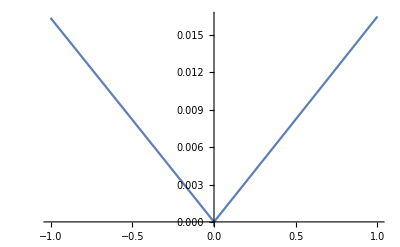

```mathematica
ListLinePlot[Transpose[{epslist,KS}],PlotRange->{Automatic,Full}]
```

```mathematica
Export[NotebookDirectory[]<>"altermu_mu[3]_1.csv",{epslist,mu3Range,matrix, KS}]
```

/home/ez/sense/benchmarks/stan_bench/altermu/altermu_mu[3]_1.csv